# Temp

### Complete Graph

```mathematica
graph=MapThread[#1<->#2&,Transpose@edges];
```

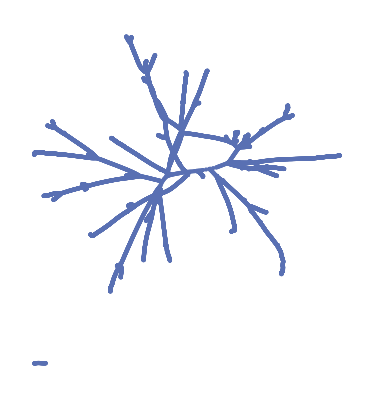

```mathematica
Graph[graph]
```

## Task 3: Transform the “cycled” graph into “tree” structure

### 1. Identify which edge should be deleted.

#### Find all meta-edge (connect component whose vertices d_G = 2)

```mathematica
loopGraph=MapThread[#1<->#2&,Transpose@loopEdges]
```

{1720<->1993,18<->6665,4967<->6665,18<->6666,4970<->6666,1710<->6667,4970<->6667,6671<->6672,4967<->6672,1694<->6673,6671<->6673,5787<->6688,5865<->6688,2327<->6689,5865<->6689,133<->6778,4919<->6778,152<->6785,1647<->6785,1671<->6809,4918<->6809,5001<->6826,5010<->6826,152<->6829,4932<->6829,4048<->6864,4090<->6864,259<->6875,1717<->6875,1698<->6876,1717<->6876,259<->6877,4986<->6877,4893<->6885,4943<->6885,298<->6900,5321<->6900,298<->6901,5322<->6901,5653<->6907,5666<->6907,5018<->6915,5338<->6915,5018<->6916,5389<->6916,2065<->6917,5338<->6917,1997<->6918,2065<->6918,342<->6938,5779<->6938,342<->6939,5968<->6939,5968<->6940,5974<->6940,5656<->6941,5974<->6941,6039<->6945,6044<->6945,344<->6946,6044<->6946,2372<->6954,5996<->6954,2138<->6958,5880<->6958,379<->6963,6118<->6963,379<->6964,6115<->6964,387<->6971,5998<->6971,402<->6982,5917<->6982,386<->6987,6344<->6987,122<->6991,6990<->6991,407<->6992,2349<->6992,2349<->6993,6096<->6993,2520<->7017,6336<->7017,5902<->7043,5943<->7043,6379<->7304,6418<->7304,700<->7356,6111<->7356,2227<->7364,5680<->7364,2227<->7365,5660<->7365,5680<->7366,5701<->7366,708<->7374,6051<->7374,708<->7375,1966<->7375,5895<->7377,7376<->7377,7376<->7378,5916<->7378,3452<->7382,7381<->7382,717<->7385,3480<->7385,3452<->7393,3483<->7393,717<->7396,3482<->7396,316<->7397,705<->7397,705<->7398,3499<->7398,316<->7400,3483<->7400,33<->7401,3482<->7401,787<->7451,5672<->7451,5671<->7452,5672<->7452,2386<->7459,2394<->7459,826<->7486,6307<->7486,6307<->7488,7487<->7488,7489<->7491,7490<->7491,7492<->7493,7489<->7493,7487<->7493,932<->7582,4933<->7582,932<->7583,1649<->7583,4889<->7619,4891<->7619,989<->7620,4998<->7620,989<->7621,5004<->7621,4958<->7634,4965<->7634,1004<->7635,4965<->7635,1005<->7636,1700<->7636,1265<->7826,5025<->7826,307<->7839,5977<->7839,2275<->7854,2367<->7854,1265<->7863,5029<->7863,5027<->7864,5029<->7864,4979<->7872,5022<->7872,4048<->7896,4924<->7896,1639<->8045,4908<->8045,1647<->8054,4933<->8054,1649<->8060,1672<->8060,4999<->8070,5000<->8070,4938<->8071,4999<->8071,1671<->8072,4917<->8072,4916<->8073,4917<->8073,1673<->8077,1702<->8077,1702<->8078,4986<->8078,1673<->8079,4987<->8079,1674<->8080,5003<->8080,270<->8081,4943<->8081,1670<->8084,4923<->8084,4923<->8085,4947<->8085,4893<->8089,4944<->8089,4968<->8092,4977<->8092,4940<->8095,4941<->8095,4891<->8098,8097<->8098,8097<->8099,4895<->8099,4101<->8101,4941<->8101,1692<->8103,8102<->8103,1693<->8104,8102<->8104,4038<->8105,4932<->8105,1695<->8106,4929<->8106,1701<->8107,4996<->8107,1697<->8108,5308<->8108,5341<->8108,1697<->8109,5337<->8109,4958<->8110,4963<->8110,4072<->8111,4963<->8111,1711<->8112,4984<->8112,4984<->8113,4992<->8113,1990<->8114,2061<->8114,2225<->8115,5315<->8115,8116<->8117,4976<->8117,4953<->8118,8116<->8118,1700<->8119,1724<->8119,1710<->8121,4953<->8121,4991<->8123,4994<->8123,4948<->8124,4991<->8124,4948<->8125,4954<->8125,1713<->8126,5002<->8126,1713<->8127,5000<->8127,4924<->8128,4934<->8128,4983<->8129,4991<->8129,4827<->8130,4949<->8130,1715<->8131,4984<->8131,1695<->8133,5001<->8133,1664<->8134,1711<->8134,1005<->8137,4955<->8137,2061<->8138,5336<->8138,1719<->8139,1984<->8139,1004<->8140,1984<->8140,4951<->8141,4955<->8141,4951<->8142,4952<->8142,5023<->8143,5037<->8143,5023<->8144,5031<->8144,1727<->8147,1766<->8147,1715<->8154,4981<->8154,4827<->8158,4992<->8158,273<->8171,5320<->8171,4553<->8173,5390<->8173,4553<->8174,5027<->8174,1754<->8176,2067<->8176,1754<->8177,5392<->8177,5392<->8178,5397<->8178,5393<->8179,5397<->8179,1728<->8183,2066<->8183,2066<->8184,4956<->8184,1760<->8186,1976<->8186,1766<->8189,5030<->8189,4962<->8191,5030<->8191,5024<->8192,5025<->8192,1342<->8193,1976<->8193,4916<->8220,4919<->8220,5677<->8308,5682<->8308,2068<->8314,2192<->8314,2068<->8315,2413<->8315,5689<->8317,5696<->8317,5328<->8322,5340<->8322,5313<->8323,5328<->8323,2023<->8324,5644<->8324,1973<->8325,1980<->8325,1980<->8326,5290<->8326,2058<->8327,5320<->8327,5290<->8331,5293<->8331,1981<->8332,5314<->8332,1988<->8337,2058<->8337,1990<->8339,5330<->8339,5317<->8340,5325<->8340,5020<->8341,5021<->8341,1999<->8344,5398<->8344,5396<->8345,5398<->8345,5312<->8346,5339<->8346,5339<->8347,5344<->8347,2418<->8360,5938<->8360,2023<->8362,5292<->8362,5286<->8363,5292<->8363,8369<->8370,5288<->8370,8369<->8371,5297<->8371,1973<->8372,5286<->8372,2228<->8375,5699<->8375,5021<->8385,5022<->8385,2063<->8387,5044<->8387,1993<->8388,5341<->8388,5395<->8389,5396<->8389,2064<->8390,5024<->8390,1997<->8391,5020<->8391,1342<->8392,5322<->8392,273<->8393,1749<->8393,1749<->8394,5336<->8394,2068<->8395,5375<->8395,2138<->8463,5782<->8463,2397<->8476,6064<->8476,2192<->8504,5670<->8504,2063<->8514,5295<->8514,5653<->8529,5671<->8529,2413<->8532,5655<->8532,2367<->8533,2370<->8533,5299<->8537,5308<->8537,2235<->8538,5692<->8538,2235<->8539,5693<->8539,1972<->8540,5692<->8540,1972<->8541,5316<->8541,2228<->8542,5698<->8542,5662<->8543,5698<->8543,2070<->8555,5028<->8555,5399<->8556,5400<->8556,2067<->8558,2070<->8558,2373<->8588,5971<->8588,2373<->8589,5960<->8589,2275<->8590,5656<->8590,6060<->8592,6063<->8592,2397<->8593,6063<->8593,2313<->8594,5860<->8594,5786<->8607,5881<->8607,5962<->8612,5963<->8612,394<->8614,8613<->8614,8613<->8615,2359<->8615,2310<->8626,5834<->8626,5834<->8627,5846<->8627,2311<->8631,5863<->8631,5862<->8632,5863<->8632,2313<->8635,5857<->8635,5857<->8636,5866<->8636,6113<->8637,6114<->8637,2317<->8641,5879<->8641,441<->8644,6088<->8644,5885<->8645,6088<->8645,6054<->8650,8649<->8650,2327<->8651,5867<->8651,2360<->8652,5782<->8652,6342<->8662,6344<->8662,2339<->8663,5787<->8663,441<->8665,6325<->8665,2342<->8666,6041<->8666,5884<->8667,6041<->8667,378<->8671,2311<->8671,716<->8673,3461<->8673,6040<->8680,6043<->8680,6039<->8681,6043<->8681,6034<->8682,6040<->8682,2351<->8689,5883<->8689,5879<->8690,5883<->8690,2351<->8691,5881<->8691,6380<->8693,8692<->8693,8692<->8694,6404<->8694,344<->8695,6036<->8695,5884<->8696,6036<->8696,2352<->8698,8697<->8698,2407<->8699,5912<->8699,5903<->8700,5912<->8700,302<->8704,5900<->8704,122<->8705,5900<->8705,2355<->8706,2440<->8706,3448<->8708,5926<->8708,3428<->8709,5909<->8709,2371<->8711,5941<->8711,3438<->8712,3444<->8712,2359<->8717,5898<->8717,386<->8718,2352<->8718,5940<->8719,5942<->8719,5887<->8720,5942<->8720,2376<->8721,5963<->8721,2368<->8722,2376<->8722,2368<->8723,5998<->8723,5809<->8725,8724<->8725,5999<->8726,8724<->8726,5779<->8727,5975<->8727,307<->8730,5781<->8730,2386<->8732,5965<->8732,2371<->8733,6001<->8733,6006<->8734,6007<->8734,2372<->8735,5997<->8735,2422<->8736,6064<->8736,5951<->8737,5969<->8737,2380<->8744,6006<->8744,6056<->8750,6057<->8750,2271<->8751,6056<->8751,5851<->8753,5866<->8753,53<->8768,2446<->8768,6990<->8775,5898<->8775,2396<->8776,6051<->8776,1966<->8790,2271<->8790,2423<->8791,5982<->8791,5970<->8792,5982<->8792,5287<->8793,5677<->8793,2424<->8794,2425<->8794,2425<->8795,5281<->8795,5281<->8796,6068<->8796,5975<->8797,5976<->8797,2427<->8798,5785<->8798,2427<->8799,5990<->8799,5990<->8800,5993<->8800,5993<->8801,6000<->8801,2434<->8804,6303<->8804,6302<->8805,6303<->8805,6332<->8812,8811<->8812,8811<->8814,8813<->8814,302<->8815,5906<->8815,2355<->8816,6104<->8816,5914<->8817,6104<->8817,2442<->8820,6302<->8820,2442<->8822,6084<->8822,6084<->8823,6120<->8823,8824<->8825,6296<->8825,6296<->8826,6297<->8826,6297<->8827,6298<->8827,2444<->8828,6089<->8828,53<->8830,8829<->8830,700<->8831,8829<->8831,5906<->8833,6110<->8833,6109<->8834,6110<->8834,6115<->8835,6123<->8835,2430<->8840,2509<->8840,6391<->8878,6393<->8878,2495<->8890,6392<->8890,2495<->8893,8892<->8893,6320<->8894,8892<->8894,2509<->8918,2535<->8918,6321<->8922,6386<->8922,6321<->8923,6322<->8923,2434<->8931,6112<->8931,404<->8932,6277<->8932,6251<->8933,6277<->8933,7492<->8934,6392<->8934,6390<->8935,6392<->8935,2518<->8936,5853<->8936,6394<->8940,6422<->8940,6390<->8943,6391<->8943,2518<->8944,5814<->8944,5814<->8945,6356<->8945,6090<->8946,6094<->8946,2520<->8949,8948<->8949,8950<->8951,8948<->8951,8950<->8952,6308<->8952,407<->8954,6091<->8954,5815<->8955,6326<->8955,6299<->8959,6300<->8959,2524<->8960,6120<->8960,2528<->8965,6597<->8965,2528<->8966,6356<->8966,5902<->8968,5940<->8968,5835<->8969,5853<->8969,2430<->8982,6278<->8982,404<->8984,6278<->8984,2535<->8985,6280<->8985,6279<->8987,6280<->8987,6404<->9000,6441<->9000,6432<->9001,6441<->9001,6397<->9002,6441<->9002,6384<->9003,6397<->9003,8604<->9009,9008<->9009,6439<->9010,9008<->9010,9029<->9030,8604<->9030,9031<->9032,9029<->9032,8988<->9033,9031<->9033,2310<->9136,5818<->9136,3320<->9663,3328<->9663,6421<->9664,6423<->9664,6422<->9665,6423<->9665,3302<->9667,3305<->9667,3290<->9677,3295<->9677,9678<->9680,9679<->9680,9681<->9682,9679<->9682,9681<->9683,6386<->9683,3295<->9688,3298<->9688,3298<->9689,3299<->9689,8813<->9691,9690<->9691,6379<->9692,9690<->9692,715<->9696,716<->9696,3290<->9698,3300<->9698,3302<->9704,3303<->9704,3305<->9705,3323<->9705,3303<->9706,3322<->9706,3300<->9707,3320<->9707,3307<->9709,3321<->9709,3321<->9710,3326<->9710,3299<->9711,3307<->9711,77<->9718,3461<->9718,715<->9723,7381<->9723,3322<->9725,6320<->9725,3323<->9726,3327<->9726,3326<->9727,3327<->9727,9728<->9729,6332<->9729,7490<->9730,9728<->9730,3297<->9733,3329<->9733,3329<->9734,3463<->9734,3297<->9735,3328<->9735,3335<->9739,6311<->9739,826<->9740,3335<->9740,6311<->9742,9741<->9742,9741<->9743,6317<->9743,6310<->9744,6317<->9744,5915<->9808,6099<->9808,402<->9809,3428<->9809,3438<->9816,3441<->9816,3442<->9817,3467<->9817,3440<->9818,3441<->9818,3439<->9819,3454<->9819,3440<->9821,3442<->9821,3443<->9824,3444<->9824,3443<->9826,9825<->9826,9825<->9827,3478<->9827,3439<->9828,3478<->9828,742<->9829,3480<->9829,3447<->9830,5927<->9830,5923<->9831,5927<->9831,3451<->9832,5895<->9832,3448<->9833,5918<->9833,3451<->9836,5933<->9836,33<->9841,3481<->9841,742<->9844,3494<->9844,77<->9846,714<->9846,714<->9847,3463<->9847,3476<->9863,3481<->9863,3454<->9864,3476<->9864,3494<->9883,3499<->9883,2000<->9974,5340<->9974,2000<->9975,5329<->9975,1720<->9976,5329<->9976,5345<->9977,5696<->9977,5700<->9978,5701<->9978,1599<->10196,5005<->10196,4038<->10204,4090<->10204,1783<->10218,4980<->10218,4981<->10219,4985<->10219,5016<->10224,5038<->10224,1694<->10232,4072<->10232,4084<->10239,5019<->10239,4979<->10240,5019<->10240,4961<->10243,4973<->10243,1268<->10247,4937<->10247,4936<->10248,4937<->10248,4930<->10249,4936<->10249,1692<->10250,4101<->10250,1686<->10268,4116<->10268,4116<->10269,4902<->10269,133<->10271,10270<->10271,1268<->10272,10270<->10272,4976<->10629,4977<->10629,4794<->10686,4978<->10686,4959<->10687,4978<->10687,4959<->10688,4971<->10688,4833<->10689,4971<->10689,4833<->10690,4975<->10690,4908<->10730,4920<->10730,10734<->10735,4921<->10735,270<->10736,4921<->10736,4894<->10737,10734<->10737,1693<->10738,4944<->10738,4894<->10739,4895<->10739,4902<->10743,4945<->10743,4942<->10744,4945<->10744,4884<->10747,4889<->10747,4884<->10748,4915<->10748,1639<->10751,4947<->10751,4880<->10752,4920<->10752,4880<->10754,4915<->10754,4918<->10756,10755<->10756,1686<->10757,10755<->10757,1672<->10758,4922<->10758,4922<->10759,4946<->10759,1670<->10762,4946<->10762,4929<->10766,5009<->10766,5009<->10767,5011<->10767,1712<->10768,5011<->10768,1712<->10769,4994<->10769,1599<->10770,4934<->10770,1674<->10771,4996<->10771,1667<->10772,5003<->10772,201<->10774,4930<->10774,4938<->10775,4939<->10775,201<->10776,4939<->10776,4983<->10777,4989<->10777,4940<->10778,4942<->10778,1664<->10779,4954<->10779,4950<->10780,4972<->10780,4956<->10781,4964<->10781,1719<->10782,4964<->10782,4961<->10783,4972<->10783,4794<->10784,4950<->10784,2064<->10786,5032<->10786,1728<->10788,4084<->10788,4968<->10790,4973<->10790,1783<->10791,4975<->10791,4974<->10792,4993<->10792,4974<->10793,4995<->10793,4949<->10794,4995<->10794,4980<->10795,4993<->10795,5036<->10796,5039<->10796,1698<->10797,5016<->10797,4989<->10798,5006<->10798,4985<->10799,4987<->10799,4998<->10803,5002<->10803,5004<->10804,5010<->10804,1701<->10805,5005<->10805,1667<->10806,5007<->10806,5006<->10807,5007<->10807,4962<->10809,5034<->10809,1727<->10810,5032<->10810,5034<->10811,5039<->10811,1724<->10813,5031<->10813,5321<->10814,5391<->10814,5390<->10815,5391<->10815,5028<->10816,5379<->10816,5036<->10817,5037<->10817,4952<->10819,5038<->10819,5044<->10824,5310<->10824,5287<->10943,5678<->10943,5678<->10944,5684<->10944,5682<->10945,6068<->10945,5295<->10951,5304<->10951,5297<->10952,5311<->10952,5298<->10953,5303<->10953,5300<->10954,5310<->10954,5299<->10955,5304<->10955,5300<->10956,5301<->10956,5301<->10957,5314<->10957,5285<->10958,5309<->10958,1981<->10959,5309<->10959,5315<->10960,5694<->10960,5303<->10962,10961<->10962,10963<->10964,10961<->10964,5288<->10965,10963<->10965,5293<->10966,5311<->10966,5330<->10969,5337<->10969,5333<->10971,5342<->10971,2208<->10972,5312<->10972,5285<->10973,5298<->10973,2225<->10974,5345<->10974,2232<->10975,5313<->10975,5662<->10976,5700<->10976,2208<->10977,5316<->10977,1994<->10980,5394<->10980,1994<->10981,5395<->10981,5332<->10982,5333<->10982,1760<->10984,1988<->10984,5326<->10985,5346<->10985,2232<->10986,5346<->10986,5327<->10987,5335<->10987,5335<->10988,5388<->10988,5324<->10990,5331<->10990,5317<->10991,5324<->10991,10992<->10993,5331<->10993,10992<->10995,10994<->10995,10994<->10996,5327<->10996,1999<->10997,5388<->10997,5325<->10998,5334<->10998,5332<->10999,5334<->10999,5340<->11000,5342<->11000,5326<->11001,5344<->11001,6071<->11021,6072<->11021,5379<->11024,5399<->11024,5389<->11025,5393<->11025,5394<->11026,5400<->11026,5652<->11160,11159<->11160,11159<->11161,6011<->11161,5665<->11162,5956<->11162,5655<->11163,5664<->11163,5664<->11164,5665<->11164,2370<->11165,5375<->11165,5679<->11167,5686<->11167,5679<->11169,11168<->11169,11170<->11171,11168<->11171,11170<->11172,5663<->11172,5956<->11175,5971<->11175,5960<->11177,5977<->11177,5660<->11178,5688<->11178,5686<->11179,5688<->11179,2424<->11181,6067<->11181,787<->11182,5663<->11182,5666<->11183,5669<->11183,5669<->11184,5670<->11184,5667<->11185,5976<->11185,5644<->11188,5684<->11188,6011<->11189,6067<->11189,5693<->11193,5694<->11193,5689<->11195,5699<->11195,5781<->11223,5972<->11223,2423<->11224,5966<->11224,5864<->11228,5882<->11228,2339<->11229,5864<->11229,2317<->11230,5882<->11230,5951<->11231,6004<->11231,5785<->11232,5969<->11232,5786<->11233,5880<->11233,6327<->11247,11246<->11247,11246<->11248,6337<->11248,6337<->11249,6338<->11249,5815<->11250,6328<->11250,6331<->11251,6380<->11251,6331<->11252,6381<->11252,6385<->11257,6394<->11257,6384<->11258,6385<->11258,5818<->11266,5835<->11266,8608<->11274,2305<->11274,378<->11275,8608<->11275,2305<->11276,5846<->11276,5851<->11279,5867<->11279,6329<->11284,6339<->11284,5885<->11285,5905<->11285,6324<->11286,6327<->11286,5860<->11287,5861<->11287,5861<->11288,5862<->11288,5905<->11289,6033<->11289,6033<->11290,6042<->11290,5901<->11291,5943<->11291,6325<->11297,6342<->11297,5887<->11298,5903<->11298,5934<->11300,5944<->11300,5886<->11301,5936<->11301,5886<->11302,5944<->11302,3447<->11308,5916<->11308,5899<->11309,5918<->11309,6099<->11311,6107<->11311,5899<->11312,5917<->11312,5901<->11313,5936<->11313,6034<->11314,6042<->11314,394<->11315,2407<->11315,6103<->11322,6107<->11322,5914<->11323,6103<->11323,3336<->11324,5919<->11324,3336<->11325,6097<->11325,5923<->11326,5928<->11326,5928<->11327,5929<->11327,5926<->11328,5929<->11328,5934<->11331,5941<->11331,5890<->11333,5935<->11333,5933<->11334,5935<->11334,3467<->11335,5890<->11335,5995<->11336,5997<->11336,5992<->11339,6001<->11339,5991<->11340,5992<->11340,387<->11342,5985<->11342,5964<->11343,5985<->11343,5955<->11344,5973<->11344,5955<->11345,5980<->11345,5964<->11346,5967<->11346,2375<->11351,5994<->11351,5994<->11352,6007<->11352,5967<->11353,5979<->11353,5957<->11354,5979<->11354,5957<->11355,5978<->11355,5978<->11356,5980<->11356,5972<->11357,5973<->11357,6069<->11358,6071<->11358,2394<->11359,5667<->11359,5652<->11362,11361<->11362,11361<->11363,6070<->11363,5970<->11364,5981<->11364,5965<->11365,5981<->11365,5991<->11366,6003<->11366,6000<->11367,6003<->11367,5962<->11368,5999<->11368,5966<->11369,5996<->11369,2375<->11371,5995<->11371,6035<->11372,6059<->11372,6035<->11373,6065<->11373,5987<->11374,6065<->11374,5987<->11375,6062<->11375,5809<->11376,6004<->11376,2360<->11377,6002<->11377,6002<->11378,6005<->11378,2380<->11379,6005<->11379,2418<->11381,6062<->11381,6038<->11387,6054<->11387,6037<->11388,6038<->11388,374<->11389,2396<->11389,2342<->11390,6037<->11390,374<->11391,8649<->11391,6059<->11395,6072<->11395,6057<->11396,6061<->11396,6060<->11397,6061<->11397,2422<->11398,5938<->11398,6069<->11399,6070<->11399,11408<->11409,2446<->11409,2436<->11410,11408<->11410,6112<->11411,6274<->11411,2436<->11417,2443<->11417,6094<->11418,6335<->11418,6091<->11419,6095<->11419,6095<->11424,11423<->11424,5892<->11425,11423<->11425,5892<->11426,6090<->11426,5915<->11427,6096<->11427,5909<->11429,6097<->11429,2440<->11430,5919<->11430,2443<->11435,2444<->11435,6089<->11436,6109<->11436,6113<->11437,6122<->11437,6111<->11439,11438<->11439,11438<->11441,11440<->11441,6114<->11442,11440<->11442,11443<->11444,8824<->11444,2524<->11452,6118<->11452,2499<->11455,6301<->11455,6122<->11456,6123<->11456,2499<->11458,11443<->11458,6251<->11577,6282<->11577,6274<->11597,6298<->11597,6276<->11600,11599<->11600,6282<->11601,11599<->11601,6276<->11605,6300<->11605,6299<->11606,6301<->11606,6309<->11610,6310<->11610,6308<->11611,6309<->11611,6322<->11615,6393<->11615,6279<->11617,11616<->11617,11616<->11619,11618<->11619,11618<->11621,11620<->11621,11620<->11622,9678<->11622,6381<->11627,6382<->11627,6330<->11628,6382<->11628,6329<->11629,6338<->11629,6326<->11630,6330<->11630,6328<->11631,6339<->11631,6335<->11636,6336<->11636,8697<->11637,6324<->11637,6601<->11661,6603<->11661,6419<->11675,6420<->11675,6418<->11676,6420<->11676,11245<->11694,11693<->11694,11693<->11695,6431<->11695,6431<->11696,6432<->11696,11245<->11698,11697<->11698,11697<->11700,11699<->11700,6419<->11708,6421<->11708,6434<->11709,6439<->11709,11699<->11711,11710<->11711,8988<->11712,11710<->11712,6434<->11719,6604<->11719,6603<->11720,6604<->11720,6597<->11832,6600<->11832,6601<->11834,6602<->11834,6602<->11836,11835<->11836,6600<->11837,11835<->11837}

```mathematica
loopGraphVertices=Union@Flatten[loopEdges]
```

{18,33,53,77,122,133,152,201,259,270,273,298,302,307,316,342,344,374,378,379,386,387,394,402,404,407,441,700,705,708,714,715,716,717,742,787,826,932,989,1004,1005,1265,1268,1342,1599,1639,1647,1649,1664,1667,1670,1671,1672,1673,1674,1686,1692,1693,1694,1695,1697,1698,1700,1701,1702,1710,1711,1712,1713,1715,1717,1719,1720,1724,1727,1728,1749,1754,1760,1766,1783,1966,1972,1973,1976,1980,1981,1984,1988,1990,1993,1994,1997,1999,2000,2023,2058,2061,2063,2064,2065,2066,2067,2068,2070,2138,2192,2208,2225,2227,2228,2232,2235,2271,2275,2305,2310,2311,2313,2317,2327,2339,2342,2349,2351,2352,2355,2359,2360,2367,2368,2370,2371,2372,2373,2375,2376,2380,2386,2394,2396,2397,2407,2413,2418,2422,2423,2424,2425,2427,2430,2434,2436,2440,2442,2443,2444,2446,2495,2499,2509,2518,2520,2524,2528,2535,3290,3295,3297,3298,3299,3300,3302,3303,3305,3307,3320,3321,3322,3323,3326,3327,3328,3329,3335,3336,3428,3438,3439,3440,3441,3442,3443,3444,3447,3448,3451,3452,3454,3461,3463,3467,3476,3478,3480,3481,3482,3483,3494,3499,4038,4048,4072,4084,4090,4101,4116,4553,4794,4827,4833,4880,4884,4889,4891,4893,4894,4895,4902,4908,4915,4916,4917,4918,4919,4920,4921,4922,4923,4924,4929,4930,4932,4933,4934,4936,4937,4938,4939,4940,4941,4942,4943,4944,4945,4946,4947,4948,4949,4950,4951,4952,4953,4954,4955,4956,4958,4959,4961,4962,4963,4964,4965,4967,4968,4970,4971,4972,4973,4974,4975,4976,4977,4978,4979,4980,4981,4983,4984,4985,4986,4987,4989,4991,4992,4993,4994,4995,4996,4998,4999,5000,5001,5002,5003,5004,5005,5006,5007,5009,5010,5011,5016,5018,5019,5020,5021,5022,5023,5024,5025,5027,5028,5029,5030,5031,5032,5034,5036,5037,5038,5039,5044,5281,5285,5286,5287,5288,5290,5292,5293,5295,5297,5298,5299,5300,5301,5303,5304,5308,5309,5310,5311,5312,5313,5314,5315,5316,5317,5320,5321,5322,5324,5325,5326,5327,5328,5329,5330,5331,5332,5333,5334,5335,5336,5337,5338,5339,5340,5341,5342,5344,5345,5346,5375,5379,5388,5389,5390,5391,5392,5393,5394,5395,5396,5397,5398,5399,5400,5644,5652,5653,5655,5656,5660,5662,5663,5664,5665,5666,5667,5669,5670,5671,5672,5677,5678,5679,5680,5682,5684,5686,5688,5689,5692,5693,5694,5696,5698,5699,5700,5701,5779,5781,5782,5785,5786,5787,5809,5814,5815,5818,5834,5835,5846,5851,5853,5857,5860,5861,5862,5863,5864,5865,5866,5867,5879,5880,5881,5882,5883,5884,5885,5886,5887,5890,5892,5895,5898,5899,5900,5901,5902,5903,5905,5906,5909,5912,5914,5915,5916,5917,5918,5919,5923,5926,5927,5928,5929,5933,5934,5935,5936,5938,5940,5941,5942,5943,5944,5951,5955,5956,5957,5960,5962,5963,5964,5965,5966,5967,5968,5969,5970,5971,5972,5973,5974,5975,5976,5977,5978,5979,5980,5981,5982,5985,5987,5990,5991,5992,5993,5994,5995,5996,5997,5998,5999,6000,6001,6002,6003,6004,6005,6006,6007,6011,6033,6034,6035,6036,6037,6038,6039,6040,6041,6042,6043,6044,6051,6054,6056,6057,6059,6060,6061,6062,6063,6064,6065,6067,6068,6069,6070,6071,6072,6084,6088,6089,6090,6091,6094,6095,6096,6097,6099,6103,6104,6107,6109,6110,6111,6112,6113,6114,6115,6118,6120,6122,6123,6251,6274,6276,6277,6278,6279,6280,6282,6296,6297,6298,6299,6300,6301,6302,6303,6307,6308,6309,6310,6311,6317,6320,6321,6322,6324,6325,6326,6327,6328,6329,6330,6331,6332,6335,6336,6337,6338,6339,6342,6344,6356,6379,6380,6381,6382,6384,6385,6386,6390,6391,6392,6393,6394,6397,6404,6418,6419,6420,6421,6422,6423,6431,6432,6434,6439,6441,6597,6600,6601,6602,6603,6604,6665,6666,6667,6671,6672,6673,6688,6689,6778,6785,6809,6826,6829,6864,6875,6876,6877,6885,6900,6901,6907,6915,6916,6917,6918,6938,6939,6940,6941,6945,6946,6954,6958,6963,6964,6971,6982,6987,6990,6991,6992,6993,7017,7043,7304,7356,7364,7365,7366,7374,7375,7376,7377,7378,7381,7382,7385,7393,7396,7397,7398,7400,7401,7451,7452,7459,7486,7487,7488,7489,7490,7491,7492,7493,7582,7583,7619,7620,7621,7634,7635,7636,7826,7839,7854,7863,7864,7872,7896,8045,8054,8060,8070,8071,8072,8073,8077,8078,8079,8080,8081,8084,8085,8089,8092,8095,8097,8098,8099,8101,8102,8103,8104,8105,8106,8107,8108,8109,8110,8111,8112,8113,8114,8115,8116,8117,8118,8119,8121,8123,8124,8125,8126,8127,8128,8129,8130,8131,8133,8134,8137,8138,8139,8140,8141,8142,8143,8144,8147,8154,8158,8171,8173,8174,8176,8177,8178,8179,8183,8184,8186,8189,8191,8192,8193,8220,8308,8314,8315,8317,8322,8323,8324,8325,8326,8327,8331,8332,8337,8339,8340,8341,8344,8345,8346,8347,8360,8362,8363,8369,8370,8371,8372,8375,8385,8387,8388,8389,8390,8391,8392,8393,8394,8395,8463,8476,8504,8514,8529,8532,8533,8537,8538,8539,8540,8541,8542,8543,8555,8556,8558,8588,8589,8590,8592,8593,8594,8604,8607,8608,8612,8613,8614,8615,8626,8627,8631,8632,8635,8636,8637,8641,8644,8645,8649,8650,8651,8652,8662,8663,8665,8666,8667,8671,8673,8680,8681,8682,8689,8690,8691,8692,8693,8694,8695,8696,8697,8698,8699,8700,8704,8705,8706,8708,8709,8711,8712,8717,8718,8719,8720,8721,8722,8723,8724,8725,8726,8727,8730,8732,8733,8734,8735,8736,8737,8744,8750,8751,8753,8768,8775,8776,8790,8791,8792,8793,8794,8795,8796,8797,8798,8799,8800,8801,8804,8805,8811,8812,8813,8814,8815,8816,8817,8820,8822,8823,8824,8825,8826,8827,8828,8829,8830,8831,8833,8834,8835,8840,8878,8890,8892,8893,8894,8918,8922,8923,8931,8932,8933,8934,8935,8936,8940,8943,8944,8945,8946,8948,8949,8950,8951,8952,8954,8955,8959,8960,8965,8966,8968,8969,8982,8984,8985,8987,8988,9000,9001,9002,9003,9008,9009,9010,9029,9030,9031,9032,9033,9136,9663,9664,9665,9667,9677,9678,9679,9680,9681,9682,9683,9688,9689,9690,9691,9692,9696,9698,9704,9705,9706,9707,9709,9710,9711,9718,9723,9725,9726,9727,9728,9729,9730,9733,9734,9735,9739,9740,9741,9742,9743,9744,9808,9809,9816,9817,9818,9819,9821,9824,9825,9826,9827,9828,9829,9830,9831,9832,9833,9836,9841,9844,9846,9847,9863,9864,9883,9974,9975,9976,9977,9978,10196,10204,10218,10219,10224,10232,10239,10240,10243,10247,10248,10249,10250,10268,10269,10270,10271,10272,10629,10686,10687,10688,10689,10690,10730,10734,10735,10736,10737,10738,10739,10743,10744,10747,10748,10751,10752,10754,10755,10756,10757,10758,10759,10762,10766,10767,10768,10769,10770,10771,10772,10774,10775,10776,10777,10778,10779,10780,10781,10782,10783,10784,10786,10788,10790,10791,10792,10793,10794,10795,10796,10797,10798,10799,10803,10804,10805,10806,10807,10809,10810,10811,10813,10814,10815,10816,10817,10819,10824,10943,10944,10945,10951,10952,10953,10954,10955,10956,10957,10958,10959,10960,10961,10962,10963,10964,10965,10966,10969,10971,10972,10973,10974,10975,10976,10977,10980,10981,10982,10984,10985,10986,10987,10988,10990,10991,10992,10993,10994,10995,10996,10997,10998,10999,11000,11001,11021,11024,11025,11026,11159,11160,11161,11162,11163,11164,11165,11167,11168,11169,11170,11171,11172,11175,11177,11178,11179,11181,11182,11183,11184,11185,11188,11189,11193,11195,11223,11224,11228,11229,11230,11231,11232,11233,11245,11246,11247,11248,11249,11250,11251,11252,11257,11258,11266,11274,11275,11276,11279,11284,11285,11286,11287,11288,11289,11290,11291,11297,11298,11300,11301,11302,11308,11309,11311,11312,11313,11314,11315,11322,11323,11324,11325,11326,11327,11328,11331,11333,11334,11335,11336,11339,11340,11342,11343,11344,11345,11346,11351,11352,11353,11354,11355,11356,11357,11358,11359,11361,11362,11363,11364,11365,11366,11367,11368,11369,11371,11372,11373,11374,11375,11376,11377,11378,11379,11381,11387,11388,11389,11390,11391,11395,11396,11397,11398,11399,11408,11409,11410,11411,11417,11418,11419,11423,11424,11425,11426,11427,11429,11430,11435,11436,11437,11438,11439,11440,11441,11442,11443,11444,11452,11455,11456,11458,11577,11597,11599,11600,11601,11605,11606,11610,11611,11615,11616,11617,11618,11619,11620,11621,11622,11627,11628,11629,11630,11631,11636,11637,11661,11675,11676,11693,11694,11695,11696,11697,11698,11699,11700,11708,11709,11710,11711,11712,11719,11720,11832,11834,11835,11836,11837}

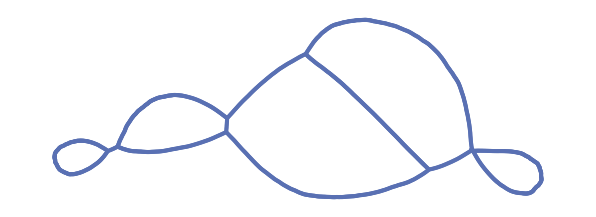

```mathematica
g=Graph[loopGraph]
```

##### Visualization with Vertex Index

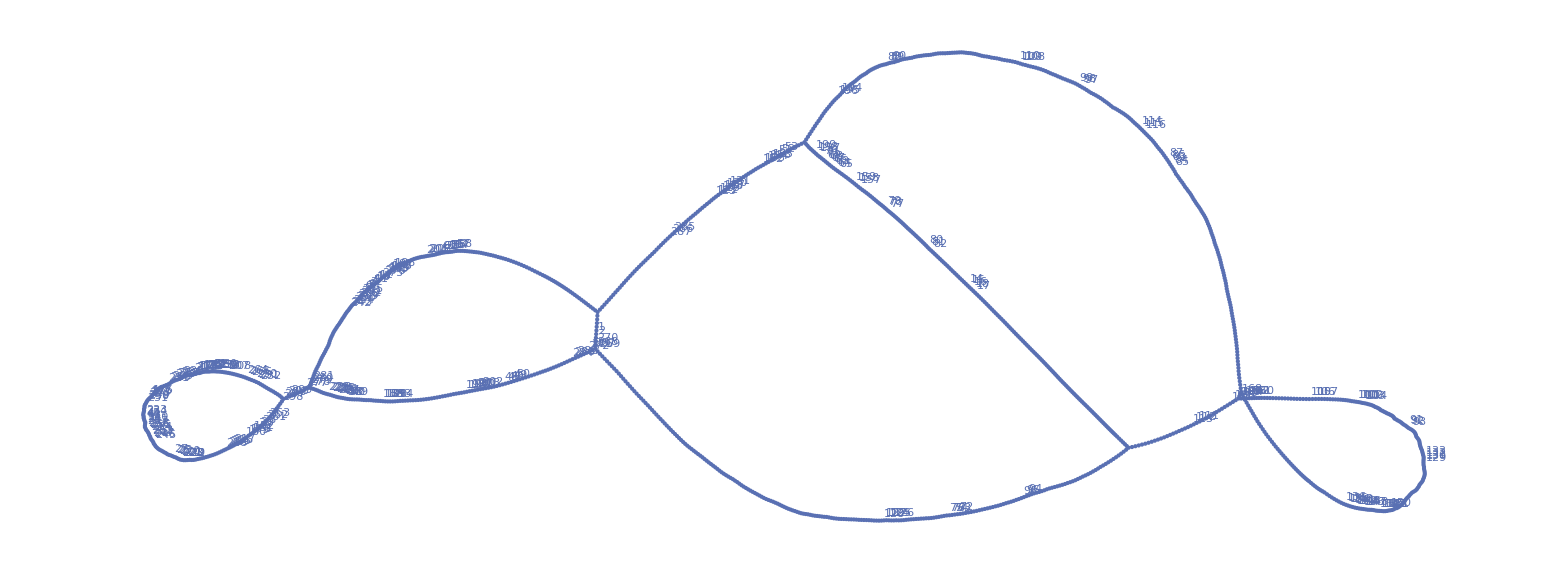

#### Find vertices whose degree d_G ≥ 3

```mathematica
vd=VertexDegree[g,#]&/@loopGraphVertices
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
pos=Flatten@Position[vd,3]
```

{104,289,294,379,651,666,746,789}

```mathematica
ShowIntersectionPointByIndex[loopGraphics, pos, vertices, loopEdges]
```

-Graphics3D-

```mathematica
degree3Vtx=loopGraphVertices⟦pos⟧
```

{2068,4984,4991,5340,6392,6441,7493,8108}

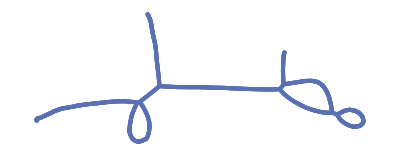
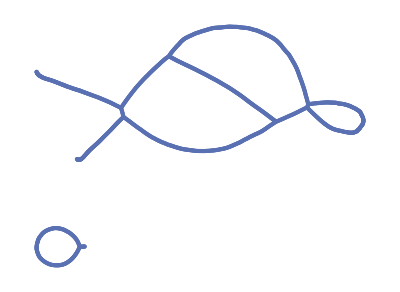
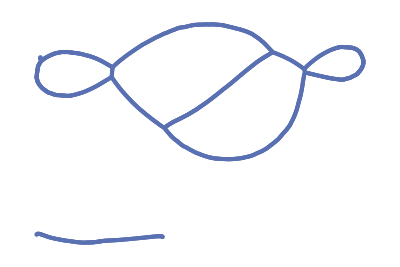
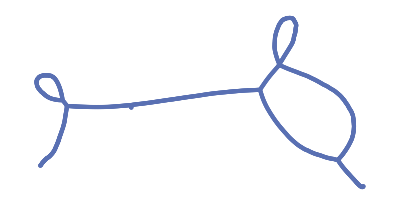
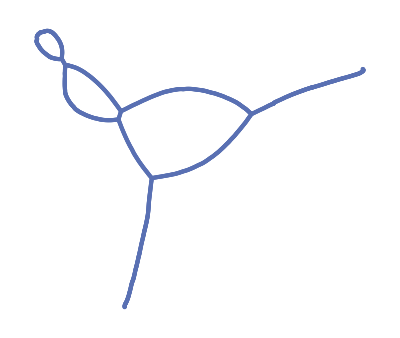
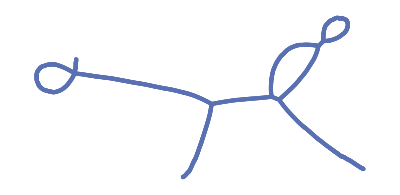
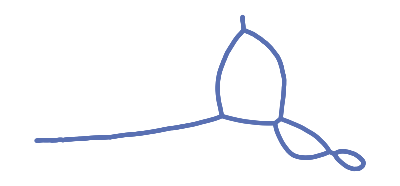
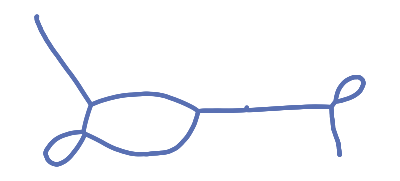

```mathematica
metaEdgesGraph=VertexDelete[loopGraph,Except[degree3Vtx,degree3Vtx⟦#⟧]]&/@Range[Length@degree3Vtx]
```

#### Stuck

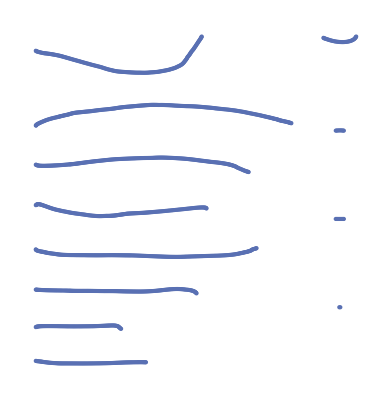

```mathematica
metaEdgesG=VertexDelete[loopGraph,degree3Vtx]
```

#### Verify this is correct

```mathematica
triEdgePosition=First@Transpose[Flatten[Position[loopEdges,#]&/@degree3Vtx,1]]
```

{316,318,386,225,226,257,240,243,253,323,841,1104,637,655,657,701,703,705,132,133,134,215,216,217}

```mathematica
metaEdgesVertices=Delete[loopGraphVertices,Position[vd,3]]
```

{18,33,53,77,122,133,152,201,259,270,273,298,302,307,316,342,344,374,378,379,386,387,394,402,404,407,441,700,705,708,714,715,716,717,742,787,826,932,989,1004,1005,1265,1268,1342,1599,1639,1647,1649,1664,1667,1670,1671,1672,1673,1674,1686,1692,1693,1694,1695,1697,1698,1700,1701,1702,1710,1711,1712,1713,1715,1717,1719,1720,1724,1727,1728,1749,1754,1760,1766,1783,1966,1972,1973,1976,1980,1981,1984,1988,1990,1993,1994,1997,1999,2000,2023,2058,2061,2063,2064,2065,2066,2067,2070,2138,2192,2208,2225,2227,2228,2232,2235,2271,2275,2305,2310,2311,2313,2317,2327,2339,2342,2349,2351,2352,2355,2359,2360,2367,2368,2370,2371,2372,2373,2375,2376,2380,2386,2394,2396,2397,2407,2413,2418,2422,2423,2424,2425,2427,2430,2434,2436,2440,2442,2443,2444,2446,2495,2499,2509,2518,2520,2524,2528,2535,3290,3295,3297,3298,3299,3300,3302,3303,3305,3307,3320,3321,3322,3323,3326,3327,3328,3329,3335,3336,3428,3438,3439,3440,3441,3442,3443,3444,3447,3448,3451,3452,3454,3461,3463,3467,3476,3478,3480,3481,3482,3483,3494,3499,4038,4048,4072,4084,4090,4101,4116,4553,4794,4827,4833,4880,4884,4889,4891,4893,4894,4895,4902,4908,4915,4916,4917,4918,4919,4920,4921,4922,4923,4924,4929,4930,4932,4933,4934,4936,4937,4938,4939,4940,4941,4942,4943,4944,4945,4946,4947,4948,4949,4950,4951,4952,4953,4954,4955,4956,4958,4959,4961,4962,4963,4964,4965,4967,4968,4970,4971,4972,4973,4974,4975,4976,4977,4978,4979,4980,4981,4983,4985,4986,4987,4989,4992,4993,4994,4995,4996,4998,4999,5000,5001,5002,5003,5004,5005,5006,5007,5009,5010,5011,5016,5018,5019,5020,5021,5022,5023,5024,5025,5027,5028,5029,5030,5031,5032,5034,5036,5037,5038,5039,5044,5281,5285,5286,5287,5288,5290,5292,5293,5295,5297,5298,5299,5300,5301,5303,5304,5308,5309,5310,5311,5312,5313,5314,5315,5316,5317,5320,5321,5322,5324,5325,5326,5327,5328,5329,5330,5331,5332,5333,5334,5335,5336,5337,5338,5339,5341,5342,5344,5345,5346,5375,5379,5388,5389,5390,5391,5392,5393,5394,5395,5396,5397,5398,5399,5400,5644,5652,5653,5655,5656,5660,5662,5663,5664,5665,5666,5667,5669,5670,5671,5672,5677,5678,5679,5680,5682,5684,5686,5688,5689,5692,5693,5694,5696,5698,5699,5700,5701,5779,5781,5782,5785,5786,5787,5809,5814,5815,5818,5834,5835,5846,5851,5853,5857,5860,5861,5862,5863,5864,5865,5866,5867,5879,5880,5881,5882,5883,5884,5885,5886,5887,5890,5892,5895,5898,5899,5900,5901,5902,5903,5905,5906,5909,5912,5914,5915,5916,5917,5918,5919,5923,5926,5927,5928,5929,5933,5934,5935,5936,5938,5940,5941,5942,5943,5944,5951,5955,5956,5957,5960,5962,5963,5964,5965,5966,5967,5968,5969,5970,5971,5972,5973,5974,5975,5976,5977,5978,5979,5980,5981,5982,5985,5987,5990,5991,5992,5993,5994,5995,5996,5997,5998,5999,6000,6001,6002,6003,6004,6005,6006,6007,6011,6033,6034,6035,6036,6037,6038,6039,6040,6041,6042,6043,6044,6051,6054,6056,6057,6059,6060,6061,6062,6063,6064,6065,6067,6068,6069,6070,6071,6072,6084,6088,6089,6090,6091,6094,6095,6096,6097,6099,6103,6104,6107,6109,6110,6111,6112,6113,6114,6115,6118,6120,6122,6123,6251,6274,6276,6277,6278,6279,6280,6282,6296,6297,6298,6299,6300,6301,6302,6303,6307,6308,6309,6310,6311,6317,6320,6321,6322,6324,6325,6326,6327,6328,6329,6330,6331,6332,6335,6336,6337,6338,6339,6342,6344,6356,6379,6380,6381,6382,6384,6385,6386,6390,6391,6393,6394,6397,6404,6418,6419,6420,6421,6422,6423,6431,6432,6434,6439,6597,6600,6601,6602,6603,6604,6665,6666,6667,6671,6672,6673,6688,6689,6778,6785,6809,6826,6829,6864,6875,6876,6877,6885,6900,6901,6907,6915,6916,6917,6918,6938,6939,6940,6941,6945,6946,6954,6958,6963,6964,6971,6982,6987,6990,6991,6992,6993,7017,7043,7304,7356,7364,7365,7366,7374,7375,7376,7377,7378,7381,7382,7385,7393,7396,7397,7398,7400,7401,7451,7452,7459,7486,7487,7488,7489,7490,7491,7492,7582,7583,7619,7620,7621,7634,7635,7636,7826,7839,7854,7863,7864,7872,7896,8045,8054,8060,8070,8071,8072,8073,8077,8078,8079,8080,8081,8084,8085,8089,8092,8095,8097,8098,8099,8101,8102,8103,8104,8105,8106,8107,8109,8110,8111,8112,8113,8114,8115,8116,8117,8118,8119,8121,8123,8124,8125,8126,8127,8128,8129,8130,8131,8133,8134,8137,8138,8139,8140,8141,8142,8143,8144,8147,8154,8158,8171,8173,8174,8176,8177,8178,8179,8183,8184,8186,8189,8191,8192,8193,8220,8308,8314,8315,8317,8322,8323,8324,8325,8326,8327,8331,8332,8337,8339,8340,8341,8344,8345,8346,8347,8360,8362,8363,8369,8370,8371,8372,8375,8385,8387,8388,8389,8390,8391,8392,8393,8394,8395,8463,8476,8504,8514,8529,8532,8533,8537,8538,8539,8540,8541,8542,8543,8555,8556,8558,8588,8589,8590,8592,8593,8594,8604,8607,8608,8612,8613,8614,8615,8626,8627,8631,8632,8635,8636,8637,8641,8644,8645,8649,8650,8651,8652,8662,8663,8665,8666,8667,8671,8673,8680,8681,8682,8689,8690,8691,8692,8693,8694,8695,8696,8697,8698,8699,8700,8704,8705,8706,8708,8709,8711,8712,8717,8718,8719,8720,8721,8722,8723,8724,8725,8726,8727,8730,8732,8733,8734,8735,8736,8737,8744,8750,8751,8753,8768,8775,8776,8790,8791,8792,8793,8794,8795,8796,8797,8798,8799,8800,8801,8804,8805,8811,8812,8813,8814,8815,8816,8817,8820,8822,8823,8824,8825,8826,8827,8828,8829,8830,8831,8833,8834,8835,8840,8878,8890,8892,8893,8894,8918,8922,8923,8931,8932,8933,8934,8935,8936,8940,8943,8944,8945,8946,8948,8949,8950,8951,8952,8954,8955,8959,8960,8965,8966,8968,8969,8982,8984,8985,8987,8988,9000,9001,9002,9003,9008,9009,9010,9029,9030,9031,9032,9033,9136,9663,9664,9665,9667,9677,9678,9679,9680,9681,9682,9683,9688,9689,9690,9691,9692,9696,9698,9704,9705,9706,9707,9709,9710,9711,9718,9723,9725,9726,9727,9728,9729,9730,9733,9734,9735,9739,9740,9741,9742,9743,9744,9808,9809,9816,9817,9818,9819,9821,9824,9825,9826,9827,9828,9829,9830,9831,9832,9833,9836,9841,9844,9846,9847,9863,9864,9883,9974,9975,9976,9977,9978,10196,10204,10218,10219,10224,10232,10239,10240,10243,10247,10248,10249,10250,10268,10269,10270,10271,10272,10629,10686,10687,10688,10689,10690,10730,10734,10735,10736,10737,10738,10739,10743,10744,10747,10748,10751,10752,10754,10755,10756,10757,10758,10759,10762,10766,10767,10768,10769,10770,10771,10772,10774,10775,10776,10777,10778,10779,10780,10781,10782,10783,10784,10786,10788,10790,10791,10792,10793,10794,10795,10796,10797,10798,10799,10803,10804,10805,10806,10807,10809,10810,10811,10813,10814,10815,10816,10817,10819,10824,10943,10944,10945,10951,10952,10953,10954,10955,10956,10957,10958,10959,10960,10961,10962,10963,10964,10965,10966,10969,10971,10972,10973,10974,10975,10976,10977,10980,10981,10982,10984,10985,10986,10987,10988,10990,10991,10992,10993,10994,10995,10996,10997,10998,10999,11000,11001,11021,11024,11025,11026,11159,11160,11161,11162,11163,11164,11165,11167,11168,11169,11170,11171,11172,11175,11177,11178,11179,11181,11182,11183,11184,11185,11188,11189,11193,11195,11223,11224,11228,11229,11230,11231,11232,11233,11245,11246,11247,11248,11249,11250,11251,11252,11257,11258,11266,11274,11275,11276,11279,11284,11285,11286,11287,11288,11289,11290,11291,11297,11298,11300,11301,11302,11308,11309,11311,11312,11313,11314,11315,11322,11323,11324,11325,11326,11327,11328,11331,11333,11334,11335,11336,11339,11340,11342,11343,11344,11345,11346,11351,11352,11353,11354,11355,11356,11357,11358,11359,11361,11362,11363,11364,11365,11366,11367,11368,11369,11371,11372,11373,11374,11375,11376,11377,11378,11379,11381,11387,11388,11389,11390,11391,11395,11396,11397,11398,11399,11408,11409,11410,11411,11417,11418,11419,11423,11424,11425,11426,11427,11429,11430,11435,11436,11437,11438,11439,11440,11441,11442,11443,11444,11452,11455,11456,11458,11577,11597,11599,11600,11601,11605,11606,11610,11611,11615,11616,11617,11618,11619,11620,11621,11622,11627,11628,11629,11630,11631,11636,11637,11661,11675,11676,11693,11694,11695,11696,11697,11698,11699,11700,11708,11709,11710,11711,11712,11719,11720,11832,11834,11835,11836,11837}

```mathematica
metaEdges=Delete[loopEdges,{#}&/@triEdgePosition]
```

{{1720,1993},{18,6665},{4967,6665},{18,6666},{4970,6666},{1710,6667},{4970,6667},{6671,6672},{4967,6672},{1694,6673},{6671,6673},{5787,6688},{5865,6688},{2327,6689},{5865,6689},{133,6778},{4919,6778},{152,6785},{1647,6785},{1671,6809},{4918,6809},{5001,6826},{5010,6826},{152,6829},{4932,6829},{4048,6864},{4090,6864},{259,6875},{1717,6875},{1698,6876},{1717,6876},{259,6877},{4986,6877},{4893,6885},{4943,6885},{298,6900},{5321,6900},{298,6901},{5322,6901},{5653,6907},{5666,6907},{5018,6915},{5338,6915},{5018,6916},{5389,6916},{2065,6917},{5338,6917},{1997,6918},{2065,6918},{342,6938},{5779,6938},{342,6939},{5968,6939},{5968,6940},{5974,6940},{5656,6941},{5974,6941},{6039,6945},{6044,6945},{344,6946},{6044,6946},{2372,6954},{5996,6954},{2138,6958},{5880,6958},{379,6963},{6118,6963},{379,6964},{6115,6964},{387,6971},{5998,6971},{402,6982},{5917,6982},{386,6987},{6344,6987},{122,6991},{6990,6991},{407,6992},{2349,6992},{2349,6993},{6096,6993},{2520,7017},{6336,7017},{5902,7043},{5943,7043},{6379,7304},{6418,7304},{700,7356},{6111,7356},{2227,7364},{5680,7364},{2227,7365},{5660,7365},{5680,7366},{5701,7366},{708,7374},{6051,7374},{708,7375},{1966,7375},{5895,7377},{7376,7377},{7376,7378},{5916,7378},{3452,7382},{7381,7382},{717,7385},{3480,7385},{3452,7393},{3483,7393},{717,7396},{3482,7396},{316,7397},{705,7397},{705,7398},{3499,7398},{316,7400},{3483,7400},{33,7401},{3482,7401},{787,7451},{5672,7451},{5671,7452},{5672,7452},{2386,7459},{2394,7459},{826,7486},{6307,7486},{6307,7488},{7487,7488},{7489,7491},{7490,7491},{932,7582},{4933,7582},{932,7583},{1649,7583},{4889,7619},{4891,7619},{989,7620},{4998,7620},{989,7621},{5004,7621},{4958,7634},{4965,7634},{1004,7635},{4965,7635},{1005,7636},{1700,7636},{1265,7826},{5025,7826},{307,7839},{5977,7839},{2275,7854},{2367,7854},{1265,7863},{5029,7863},{5027,7864},{5029,7864},{4979,7872},{5022,7872},{4048,7896},{4924,7896},{1639,8045},{4908,8045},{1647,8054},{4933,8054},{1649,8060},{1672,8060},{4999,8070},{5000,8070},{4938,8071},{4999,8071},{1671,8072},{4917,8072},{4916,8073},{4917,8073},{1673,8077},{1702,8077},{1702,8078},{4986,8078},{1673,8079},{4987,8079},{1674,8080},{5003,8080},{270,8081},{4943,8081},{1670,8084},{4923,8084},{4923,8085},{4947,8085},{4893,8089},{4944,8089},{4968,8092},{4977,8092},{4940,8095},{4941,8095},{4891,8098},{8097,8098},{8097,8099},{4895,8099},{4101,8101},{4941,8101},{1692,8103},{8102,8103},{1693,8104},{8102,8104},{4038,8105},{4932,8105},{1695,8106},{4929,8106},{1701,8107},{4996,8107},{1697,8109},{5337,8109},{4958,8110},{4963,8110},{4072,8111},{4963,8111},{1711,8112},{4992,8113},{1990,8114},{2061,8114},{2225,8115},{5315,8115},{8116,8117},{4976,8117},{4953,8118},{8116,8118},{1700,8119},{1724,8119},{1710,8121},{4953,8121},{4994,8123},{4948,8124},{4948,8125},{4954,8125},{1713,8126},{5002,8126},{1713,8127},{5000,8127},{4924,8128},{4934,8128},{4983,8129},{4827,8130},{4949,8130},{1715,8131},{1695,8133},{5001,8133},{1664,8134},{1711,8134},{1005,8137},{4955,8137},{2061,8138},{5336,8138},{1719,8139},{1984,8139},{1004,8140},{1984,8140},{4951,8141},{4955,8141},{4951,8142},{4952,8142},{5023,8143},{5037,8143},{5023,8144},{5031,8144},{1727,8147},{1766,8147},{1715,8154},{4981,8154},{4827,8158},{4992,8158},{273,8171},{5320,8171},{4553,8173},{5390,8173},{4553,8174},{5027,8174},{1754,8176},{2067,8176},{1754,8177},{5392,8177},{5392,8178},{5397,8178},{5393,8179},{5397,8179},{1728,8183},{2066,8183},{2066,8184},{4956,8184},{1760,8186},{1976,8186},{1766,8189},{5030,8189},{4962,8191},{5030,8191},{5024,8192},{5025,8192},{1342,8193},{1976,8193},{4916,8220},{4919,8220},{5677,8308},{5682,8308},{2192,8314},{2413,8315},{5689,8317},{5696,8317},{5328,8322},{5313,8323},{5328,8323},{2023,8324},{5644,8324},{1973,8325},{1980,8325},{1980,8326},{5290,8326},{2058,8327},{5320,8327},{5290,8331},{5293,8331},{1981,8332},{5314,8332},{1988,8337},{2058,8337},{1990,8339},{5330,8339},{5317,8340},{5325,8340},{5020,8341},{5021,8341},{1999,8344},{5398,8344},{5396,8345},{5398,8345},{5312,8346},{5339,8346},{5339,8347},{5344,8347},{2418,8360},{5938,8360},{2023,8362},{5292,8362},{5286,8363},{5292,8363},{8369,8370},{5288,8370},{8369,8371},{5297,8371},{1973,8372},{5286,8372},{2228,8375},{5699,8375},{5021,8385},{5022,8385},{2063,8387},{5044,8387},{1993,8388},{5341,8388},{5395,8389},{5396,8389},{2064,8390},{5024,8390},{1997,8391},{5020,8391},{1342,8392},{5322,8392},{273,8393},{1749,8393},{1749,8394},{5336,8394},{5375,8395},{2138,8463},{5782,8463},{2397,8476},{6064,8476},{2192,8504},{5670,8504},{2063,8514},{5295,8514},{5653,8529},{5671,8529},{2413,8532},{5655,8532},{2367,8533},{2370,8533},{5299,8537},{5308,8537},{2235,8538},{5692,8538},{2235,8539},{5693,8539},{1972,8540},{5692,8540},{1972,8541},{5316,8541},{2228,8542},{5698,8542},{5662,8543},{5698,8543},{2070,8555},{5028,8555},{5399,8556},{5400,8556},{2067,8558},{2070,8558},{2373,8588},{5971,8588},{2373,8589},{5960,8589},{2275,8590},{5656,8590},{6060,8592},{6063,8592},{2397,8593},{6063,8593},{2313,8594},{5860,8594},{5786,8607},{5881,8607},{5962,8612},{5963,8612},{394,8614},{8613,8614},{8613,8615},{2359,8615},{2310,8626},{5834,8626},{5834,8627},{5846,8627},{2311,8631},{5863,8631},{5862,8632},{5863,8632},{2313,8635},{5857,8635},{5857,8636},{5866,8636},{6113,8637},{6114,8637},{2317,8641},{5879,8641},{441,8644},{6088,8644},{5885,8645},{6088,8645},{6054,8650},{8649,8650},{2327,8651},{5867,8651},{2360,8652},{5782,8652},{6342,8662},{6344,8662},{2339,8663},{5787,8663},{441,8665},{6325,8665},{2342,8666},{6041,8666},{5884,8667},{6041,8667},{378,8671},{2311,8671},{716,8673},{3461,8673},{6040,8680},{6043,8680},{6039,8681},{6043,8681},{6034,8682},{6040,8682},{2351,8689},{5883,8689},{5879,8690},{5883,8690},{2351,8691},{5881,8691},{6380,8693},{8692,8693},{8692,8694},{6404,8694},{344,8695},{6036,8695},{5884,8696},{6036,8696},{2352,8698},{8697,8698},{2407,8699},{5912,8699},{5903,8700},{5912,8700},{302,8704},{5900,8704},{122,8705},{5900,8705},{2355,8706},{2440,8706},{3448,8708},{5926,8708},{3428,8709},{5909,8709},{2371,8711},{5941,8711},{3438,8712},{3444,8712},{2359,8717},{5898,8717},{386,8718},{2352,8718},{5940,8719},{5942,8719},{5887,8720},{5942,8720},{2376,8721},{5963,8721},{2368,8722},{2376,8722},{2368,8723},{5998,8723},{5809,8725},{8724,8725},{5999,8726},{8724,8726},{5779,8727},{5975,8727},{307,8730},{5781,8730},{2386,8732},{5965,8732},{2371,8733},{6001,8733},{6006,8734},{6007,8734},{2372,8735},{5997,8735},{2422,8736},{6064,8736},{5951,8737},{5969,8737},{2380,8744},{6006,8744},{6056,8750},{6057,8750},{2271,8751},{6056,8751},{5851,8753},{5866,8753},{53,8768},{2446,8768},{6990,8775},{5898,8775},{2396,8776},{6051,8776},{1966,8790},{2271,8790},{2423,8791},{5982,8791},{5970,8792},{5982,8792},{5287,8793},{5677,8793},{2424,8794},{2425,8794},{2425,8795},{5281,8795},{5281,8796},{6068,8796},{5975,8797},{5976,8797},{2427,8798},{5785,8798},{2427,8799},{5990,8799},{5990,8800},{5993,8800},{5993,8801},{6000,8801},{2434,8804},{6303,8804},{6302,8805},{6303,8805},{6332,8812},{8811,8812},{8811,8814},{8813,8814},{302,8815},{5906,8815},{2355,8816},{6104,8816},{5914,8817},{6104,8817},{2442,8820},{6302,8820},{2442,8822},{6084,8822},{6084,8823},{6120,8823},{8824,8825},{6296,8825},{6296,8826},{6297,8826},{6297,8827},{6298,8827},{2444,8828},{6089,8828},{53,8830},{8829,8830},{700,8831},{8829,8831},{5906,8833},{6110,8833},{6109,8834},{6110,8834},{6115,8835},{6123,8835},{2430,8840},{2509,8840},{6391,8878},{6393,8878},{2495,8890},{2495,8893},{8892,8893},{6320,8894},{8892,8894},{2509,8918},{2535,8918},{6321,8922},{6386,8922},{6321,8923},{6322,8923},{2434,8931},{6112,8931},{404,8932},{6277,8932},{6251,8933},{6277,8933},{7492,8934},{6390,8935},{2518,8936},{5853,8936},{6394,8940},{6422,8940},{6390,8943},{6391,8943},{2518,8944},{5814,8944},{5814,8945},{6356,8945},{6090,8946},{6094,8946},{2520,8949},{8948,8949},{8950,8951},{8948,8951},{8950,8952},{6308,8952},{407,8954},{6091,8954},{5815,8955},{6326,8955},{6299,8959},{6300,8959},{2524,8960},{6120,8960},{2528,8965},{6597,8965},{2528,8966},{6356,8966},{5902,8968},{5940,8968},{5835,8969},{5853,8969},{2430,8982},{6278,8982},{404,8984},{6278,8984},{2535,8985},{6280,8985},{6279,8987},{6280,8987},{6404,9000},{6432,9001},{6397,9002},{6384,9003},{6397,9003},{8604,9009},{9008,9009},{6439,9010},{9008,9010},{9029,9030},{8604,9030},{9031,9032},{9029,9032},{8988,9033},{9031,9033},{2310,9136},{5818,9136},{3320,9663},{3328,9663},{6421,9664},{6423,9664},{6422,9665},{6423,9665},{3302,9667},{3305,9667},{3290,9677},{3295,9677},{9678,9680},{9679,9680},{9681,9682},{9679,9682},{9681,9683},{6386,9683},{3295,9688},{3298,9688},{3298,9689},{3299,9689},{8813,9691},{9690,9691},{6379,9692},{9690,9692},{715,9696},{716,9696},{3290,9698},{3300,9698},{3302,9704},{3303,9704},{3305,9705},{3323,9705},{3303,9706},{3322,9706},{3300,9707},{3320,9707},{3307,9709},{3321,9709},{3321,9710},{3326,9710},{3299,9711},{3307,9711},{77,9718},{3461,9718},{715,9723},{7381,9723},{3322,9725},{6320,9725},{3323,9726},{3327,9726},{3326,9727},{3327,9727},{9728,9729},{6332,9729},{7490,9730},{9728,9730},{3297,9733},{3329,9733},{3329,9734},{3463,9734},{3297,9735},{3328,9735},{3335,9739},{6311,9739},{826,9740},{3335,9740},{6311,9742},{9741,9742},{9741,9743},{6317,9743},{6310,9744},{6317,9744},{5915,9808},{6099,9808},{402,9809},{3428,9809},{3438,9816},{3441,9816},{3442,9817},{3467,9817},{3440,9818},{3441,9818},{3439,9819},{3454,9819},{3440,9821},{3442,9821},{3443,9824},{3444,9824},{3443,9826},{9825,9826},{9825,9827},{3478,9827},{3439,9828},{3478,9828},{742,9829},{3480,9829},{3447,9830},{5927,9830},{5923,9831},{5927,9831},{3451,9832},{5895,9832},{3448,9833},{5918,9833},{3451,9836},{5933,9836},{33,9841},{3481,9841},{742,9844},{3494,9844},{77,9846},{714,9846},{714,9847},{3463,9847},{3476,9863},{3481,9863},{3454,9864},{3476,9864},{3494,9883},{3499,9883},{2000,9974},{2000,9975},{5329,9975},{1720,9976},{5329,9976},{5345,9977},{5696,9977},{5700,9978},{5701,9978},{1599,10196},{5005,10196},{4038,10204},{4090,10204},{1783,10218},{4980,10218},{4981,10219},{4985,10219},{5016,10224},{5038,10224},{1694,10232},{4072,10232},{4084,10239},{5019,10239},{4979,10240},{5019,10240},{4961,10243},{4973,10243},{1268,10247},{4937,10247},{4936,10248},{4937,10248},{4930,10249},{4936,10249},{1692,10250},{4101,10250},{1686,10268},{4116,10268},{4116,10269},{4902,10269},{133,10271},{10270,10271},{1268,10272},{10270,10272},{4976,10629},{4977,10629},{4794,10686},{4978,10686},{4959,10687},{4978,10687},{4959,10688},{4971,10688},{4833,10689},{4971,10689},{4833,10690},{4975,10690},{4908,10730},{4920,10730},{10734,10735},{4921,10735},{270,10736},{4921,10736},{4894,10737},{10734,10737},{1693,10738},{4944,10738},{4894,10739},{4895,10739},{4902,10743},{4945,10743},{4942,10744},{4945,10744},{4884,10747},{4889,10747},{4884,10748},{4915,10748},{1639,10751},{4947,10751},{4880,10752},{4920,10752},{4880,10754},{4915,10754},{4918,10756},{10755,10756},{1686,10757},{10755,10757},{1672,10758},{4922,10758},{4922,10759},{4946,10759},{1670,10762},{4946,10762},{4929,10766},{5009,10766},{5009,10767},{5011,10767},{1712,10768},{5011,10768},{1712,10769},{4994,10769},{1599,10770},{4934,10770},{1674,10771},{4996,10771},{1667,10772},{5003,10772},{201,10774},{4930,10774},{4938,10775},{4939,10775},{201,10776},{4939,10776},{4983,10777},{4989,10777},{4940,10778},{4942,10778},{1664,10779},{4954,10779},{4950,10780},{4972,10780},{4956,10781},{4964,10781},{1719,10782},{4964,10782},{4961,10783},{4972,10783},{4794,10784},{4950,10784},{2064,10786},{5032,10786},{1728,10788},{4084,10788},{4968,10790},{4973,10790},{1783,10791},{4975,10791},{4974,10792},{4993,10792},{4974,10793},{4995,10793},{4949,10794},{4995,10794},{4980,10795},{4993,10795},{5036,10796},{5039,10796},{1698,10797},{5016,10797},{4989,10798},{5006,10798},{4985,10799},{4987,10799},{4998,10803},{5002,10803},{5004,10804},{5010,10804},{1701,10805},{5005,10805},{1667,10806},{5007,10806},{5006,10807},{5007,10807},{4962,10809},{5034,10809},{1727,10810},{5032,10810},{5034,10811},{5039,10811},{1724,10813},{5031,10813},{5321,10814},{5391,10814},{5390,10815},{5391,10815},{5028,10816},{5379,10816},{5036,10817},{5037,10817},{4952,10819},{5038,10819},{5044,10824},{5310,10824},{5287,10943},{5678,10943},{5678,10944},{5684,10944},{5682,10945},{6068,10945},{5295,10951},{5304,10951},{5297,10952},{5311,10952},{5298,10953},{5303,10953},{5300,10954},{5310,10954},{5299,10955},{5304,10955},{5300,10956},{5301,10956},{5301,10957},{5314,10957},{5285,10958},{5309,10958},{1981,10959},{5309,10959},{5315,10960},{5694,10960},{5303,10962},{10961,10962},{10963,10964},{10961,10964},{5288,10965},{10963,10965},{5293,10966},{5311,10966},{5330,10969},{5337,10969},{5333,10971},{5342,10971},{2208,10972},{5312,10972},{5285,10973},{5298,10973},{2225,10974},{5345,10974},{2232,10975},{5313,10975},{5662,10976},{5700,10976},{2208,10977},{5316,10977},{1994,10980},{5394,10980},{1994,10981},{5395,10981},{5332,10982},{5333,10982},{1760,10984},{1988,10984},{5326,10985},{5346,10985},{2232,10986},{5346,10986},{5327,10987},{5335,10987},{5335,10988},{5388,10988},{5324,10990},{5331,10990},{5317,10991},{5324,10991},{10992,10993},{5331,10993},{10992,10995},{10994,10995},{10994,10996},{5327,10996},{1999,10997},{5388,10997},{5325,10998},{5334,10998},{5332,10999},{5334,10999},{5342,11000},{5326,11001},{5344,11001},{6071,11021},{6072,11021},{5379,11024},{5399,11024},{5389,11025},{5393,11025},{5394,11026},{5400,11026},{5652,11160},{11159,11160},{11159,11161},{6011,11161},{5665,11162},{5956,11162},{5655,11163},{5664,11163},{5664,11164},{5665,11164},{2370,11165},{5375,11165},{5679,11167},{5686,11167},{5679,11169},{11168,11169},{11170,11171},{11168,11171},{11170,11172},{5663,11172},{5956,11175},{5971,11175},{5960,11177},{5977,11177},{5660,11178},{5688,11178},{5686,11179},{5688,11179},{2424,11181},{6067,11181},{787,11182},{5663,11182},{5666,11183},{5669,11183},{5669,11184},{5670,11184},{5667,11185},{5976,11185},{5644,11188},{5684,11188},{6011,11189},{6067,11189},{5693,11193},{5694,11193},{5689,11195},{5699,11195},{5781,11223},{5972,11223},{2423,11224},{5966,11224},{5864,11228},{5882,11228},{2339,11229},{5864,11229},{2317,11230},{5882,11230},{5951,11231},{6004,11231},{5785,11232},{5969,11232},{5786,11233},{5880,11233},{6327,11247},{11246,11247},{11246,11248},{6337,11248},{6337,11249},{6338,11249},{5815,11250},{6328,11250},{6331,11251},{6380,11251},{6331,11252},{6381,11252},{6385,11257},{6394,11257},{6384,11258},{6385,11258},{5818,11266},{5835,11266},{8608,11274},{2305,11274},{378,11275},{8608,11275},{2305,11276},{5846,11276},{5851,11279},{5867,11279},{6329,11284},{6339,11284},{5885,11285},{5905,11285},{6324,11286},{6327,11286},{5860,11287},{5861,11287},{5861,11288},{5862,11288},{5905,11289},{6033,11289},{6033,11290},{6042,11290},{5901,11291},{5943,11291},{6325,11297},{6342,11297},{5887,11298},{5903,11298},{5934,11300},{5944,11300},{5886,11301},{5936,11301},{5886,11302},{5944,11302},{3447,11308},{5916,11308},{5899,11309},{5918,11309},{6099,11311},{6107,11311},{5899,11312},{5917,11312},{5901,11313},{5936,11313},{6034,11314},{6042,11314},{394,11315},{2407,11315},{6103,11322},{6107,11322},{5914,11323},{6103,11323},{3336,11324},{5919,11324},{3336,11325},{6097,11325},{5923,11326},{5928,11326},{5928,11327},{5929,11327},{5926,11328},{5929,11328},{5934,11331},{5941,11331},{5890,11333},{5935,11333},{5933,11334},{5935,11334},{3467,11335},{5890,11335},{5995,11336},{5997,11336},{5992,11339},{6001,11339},{5991,11340},{5992,11340},{387,11342},{5985,11342},{5964,11343},{5985,11343},{5955,11344},{5973,11344},{5955,11345},{5980,11345},{5964,11346},{5967,11346},{2375,11351},{5994,11351},{5994,11352},{6007,11352},{5967,11353},{5979,11353},{5957,11354},{5979,11354},{5957,11355},{5978,11355},{5978,11356},{5980,11356},{5972,11357},{5973,11357},{6069,11358},{6071,11358},{2394,11359},{5667,11359},{5652,11362},{11361,11362},{11361,11363},{6070,11363},{5970,11364},{5981,11364},{5965,11365},{5981,11365},{5991,11366},{6003,11366},{6000,11367},{6003,11367},{5962,11368},{5999,11368},{5966,11369},{5996,11369},{2375,11371},{5995,11371},{6035,11372},{6059,11372},{6035,11373},{6065,11373},{5987,11374},{6065,11374},{5987,11375},{6062,11375},{5809,11376},{6004,11376},{2360,11377},{6002,11377},{6002,11378},{6005,11378},{2380,11379},{6005,11379},{2418,11381},{6062,11381},{6038,11387},{6054,11387},{6037,11388},{6038,11388},{374,11389},{2396,11389},{2342,11390},{6037,11390},{374,11391},{8649,11391},{6059,11395},{6072,11395},{6057,11396},{6061,11396},{6060,11397},{6061,11397},{2422,11398},{5938,11398},{6069,11399},{6070,11399},{11408,11409},{2446,11409},{2436,11410},{11408,11410},{6112,11411},{6274,11411},{2436,11417},{2443,11417},{6094,11418},{6335,11418},{6091,11419},{6095,11419},{6095,11424},{11423,11424},{5892,11425},{11423,11425},{5892,11426},{6090,11426},{5915,11427},{6096,11427},{5909,11429},{6097,11429},{2440,11430},{5919,11430},{2443,11435},{2444,11435},{6089,11436},{6109,11436},{6113,11437},{6122,11437},{6111,11439},{11438,11439},{11438,11441},{11440,11441},{6114,11442},{11440,11442},{11443,11444},{8824,11444},{2524,11452},{6118,11452},{2499,11455},{6301,11455},{6122,11456},{6123,11456},{2499,11458},{11443,11458},{6251,11577},{6282,11577},{6274,11597},{6298,11597},{6276,11600},{11599,11600},{6282,11601},{11599,11601},{6276,11605},{6300,11605},{6299,11606},{6301,11606},{6309,11610},{6310,11610},{6308,11611},{6309,11611},{6322,11615},{6393,11615},{6279,11617},{11616,11617},{11616,11619},{11618,11619},{11618,11621},{11620,11621},{11620,11622},{9678,11622},{6381,11627},{6382,11627},{6330,11628},{6382,11628},{6329,11629},{6338,11629},{6326,11630},{6330,11630},{6328,11631},{6339,11631},{6335,11636},{6336,11636},{8697,11637},{6324,11637},{6601,11661},{6603,11661},{6419,11675},{6420,11675},{6418,11676},{6420,11676},{11245,11694},{11693,11694},{11693,11695},{6431,11695},{6431,11696},{6432,11696},{11245,11698},{11697,11698},{11697,11700},{11699,11700},{6419,11708},{6421,11708},{6434,11709},{6439,11709},{11699,11711},{11710,11711},{8988,11712},{11710,11712},{6434,11719},{6604,11719},{6603,11720},{6604,11720},{6597,11832},{6600,11832},{6601,11834},{6602,11834},{6602,11836},{11835,11836},{6600,11837},{11835,11837}}

```mathematica
metaGraph=MapThread[#1<->#2&,Transpose@metaEdges]
```

{1720<->1993,18<->6665,4967<->6665,18<->6666,4970<->6666,1710<->6667,4970<->6667,6671<->6672,4967<->6672,1694<->6673,6671<->6673,5787<->6688,5865<->6688,2327<->6689,5865<->6689,133<->6778,4919<->6778,152<->6785,1647<->6785,1671<->6809,4918<->6809,5001<->6826,5010<->6826,152<->6829,4932<->6829,4048<->6864,4090<->6864,259<->6875,1717<->6875,1698<->6876,1717<->6876,259<->6877,4986<->6877,4893<->6885,4943<->6885,298<->6900,5321<->6900,298<->6901,5322<->6901,5653<->6907,5666<->6907,5018<->6915,5338<->6915,5018<->6916,5389<->6916,2065<->6917,5338<->6917,1997<->6918,2065<->6918,342<->6938,5779<->6938,342<->6939,5968<->6939,5968<->6940,5974<->6940,5656<->6941,5974<->6941,6039<->6945,6044<->6945,344<->6946,6044<->6946,2372<->6954,5996<->6954,2138<->6958,5880<->6958,379<->6963,6118<->6963,379<->6964,6115<->6964,387<->6971,5998<->6971,402<->6982,5917<->6982,386<->6987,6344<->6987,122<->6991,6990<->6991,407<->6992,2349<->6992,2349<->6993,6096<->6993,2520<->7017,6336<->7017,5902<->7043,5943<->7043,6379<->7304,6418<->7304,700<->7356,6111<->7356,2227<->7364,5680<->7364,2227<->7365,5660<->7365,5680<->7366,5701<->7366,708<->7374,6051<->7374,708<->7375,1966<->7375,5895<->7377,7376<->7377,7376<->7378,5916<->7378,3452<->7382,7381<->7382,717<->7385,3480<->7385,3452<->7393,3483<->7393,717<->7396,3482<->7396,316<->7397,705<->7397,705<->7398,3499<->7398,316<->7400,3483<->7400,33<->7401,3482<->7401,787<->7451,5672<->7451,5671<->7452,5672<->7452,2386<->7459,2394<->7459,826<->7486,6307<->7486,6307<->7488,7487<->7488,7489<->7491,7490<->7491,932<->7582,4933<->7582,932<->7583,1649<->7583,4889<->7619,4891<->7619,989<->7620,4998<->7620,989<->7621,5004<->7621,4958<->7634,4965<->7634,1004<->7635,4965<->7635,1005<->7636,1700<->7636,1265<->7826,5025<->7826,307<->7839,5977<->7839,2275<->7854,2367<->7854,1265<->7863,5029<->7863,5027<->7864,5029<->7864,4979<->7872,5022<->7872,4048<->7896,4924<->7896,1639<->8045,4908<->8045,1647<->8054,4933<->8054,1649<->8060,1672<->8060,4999<->8070,5000<->8070,4938<->8071,4999<->8071,1671<->8072,4917<->8072,4916<->8073,4917<->8073,1673<->8077,1702<->8077,1702<->8078,4986<->8078,1673<->8079,4987<->8079,1674<->8080,5003<->8080,270<->8081,4943<->8081,1670<->8084,4923<->8084,4923<->8085,4947<->8085,4893<->8089,4944<->8089,4968<->8092,4977<->8092,4940<->8095,4941<->8095,4891<->8098,8097<->8098,8097<->8099,4895<->8099,4101<->8101,4941<->8101,1692<->8103,8102<->8103,1693<->8104,8102<->8104,4038<->8105,4932<->8105,1695<->8106,4929<->8106,1701<->8107,4996<->8107,1697<->8109,5337<->8109,4958<->8110,4963<->8110,4072<->8111,4963<->8111,1711<->8112,4992<->8113,1990<->8114,2061<->8114,2225<->8115,5315<->8115,8116<->8117,4976<->8117,4953<->8118,8116<->8118,1700<->8119,1724<->8119,1710<->8121,4953<->8121,4994<->8123,4948<->8124,4948<->8125,4954<->8125,1713<->8126,5002<->8126,1713<->8127,5000<->8127,4924<->8128,4934<->8128,4983<->8129,4827<->8130,4949<->8130,1715<->8131,1695<->8133,5001<->8133,1664<->8134,1711<->8134,1005<->8137,4955<->8137,2061<->8138,5336<->8138,1719<->8139,1984<->8139,1004<->8140,1984<->8140,4951<->8141,4955<->8141,4951<->8142,4952<->8142,5023<->8143,5037<->8143,5023<->8144,5031<->8144,1727<->8147,1766<->8147,1715<->8154,4981<->8154,4827<->8158,4992<->8158,273<->8171,5320<->8171,4553<->8173,5390<->8173,4553<->8174,5027<->8174,1754<->8176,2067<->8176,1754<->8177,5392<->8177,5392<->8178,5397<->8178,5393<->8179,5397<->8179,1728<->8183,2066<->8183,2066<->8184,4956<->8184,1760<->8186,1976<->8186,1766<->8189,5030<->8189,4962<->8191,5030<->8191,5024<->8192,5025<->8192,1342<->8193,1976<->8193,4916<->8220,4919<->8220,5677<->8308,5682<->8308,2192<->8314,2413<->8315,5689<->8317,5696<->8317,5328<->8322,5313<->8323,5328<->8323,2023<->8324,5644<->8324,1973<->8325,1980<->8325,1980<->8326,5290<->8326,2058<->8327,5320<->8327,5290<->8331,5293<->8331,1981<->8332,5314<->8332,1988<->8337,2058<->8337,1990<->8339,5330<->8339,5317<->8340,5325<->8340,5020<->8341,5021<->8341,1999<->8344,5398<->8344,5396<->8345,5398<->8345,5312<->8346,5339<->8346,5339<->8347,5344<->8347,2418<->8360,5938<->8360,2023<->8362,5292<->8362,5286<->8363,5292<->8363,8369<->8370,5288<->8370,8369<->8371,5297<->8371,1973<->8372,5286<->8372,2228<->8375,5699<->8375,5021<->8385,5022<->8385,2063<->8387,5044<->8387,1993<->8388,5341<->8388,5395<->8389,5396<->8389,2064<->8390,5024<->8390,1997<->8391,5020<->8391,1342<->8392,5322<->8392,273<->8393,1749<->8393,1749<->8394,5336<->8394,5375<->8395,2138<->8463,5782<->8463,2397<->8476,6064<->8476,2192<->8504,5670<->8504,2063<->8514,5295<->8514,5653<->8529,5671<->8529,2413<->8532,5655<->8532,2367<->8533,2370<->8533,5299<->8537,5308<->8537,2235<->8538,5692<->8538,2235<->8539,5693<->8539,1972<->8540,5692<->8540,1972<->8541,5316<->8541,2228<->8542,5698<->8542,5662<->8543,5698<->8543,2070<->8555,5028<->8555,5399<->8556,5400<->8556,2067<->8558,2070<->8558,2373<->8588,5971<->8588,2373<->8589,5960<->8589,2275<->8590,5656<->8590,6060<->8592,6063<->8592,2397<->8593,6063<->8593,2313<->8594,5860<->8594,5786<->8607,5881<->8607,5962<->8612,5963<->8612,394<->8614,8613<->8614,8613<->8615,2359<->8615,2310<->8626,5834<->8626,5834<->8627,5846<->8627,2311<->8631,5863<->8631,5862<->8632,5863<->8632,2313<->8635,5857<->8635,5857<->8636,5866<->8636,6113<->8637,6114<->8637,2317<->8641,5879<->8641,441<->8644,6088<->8644,5885<->8645,6088<->8645,6054<->8650,8649<->8650,2327<->8651,5867<->8651,2360<->8652,5782<->8652,6342<->8662,6344<->8662,2339<->8663,5787<->8663,441<->8665,6325<->8665,2342<->8666,6041<->8666,5884<->8667,6041<->8667,378<->8671,2311<->8671,716<->8673,3461<->8673,6040<->8680,6043<->8680,6039<->8681,6043<->8681,6034<->8682,6040<->8682,2351<->8689,5883<->8689,5879<->8690,5883<->8690,2351<->8691,5881<->8691,6380<->8693,8692<->8693,8692<->8694,6404<->8694,344<->8695,6036<->8695,5884<->8696,6036<->8696,2352<->8698,8697<->8698,2407<->8699,5912<->8699,5903<->8700,5912<->8700,302<->8704,5900<->8704,122<->8705,5900<->8705,2355<->8706,2440<->8706,3448<->8708,5926<->8708,3428<->8709,5909<->8709,2371<->8711,5941<->8711,3438<->8712,3444<->8712,2359<->8717,5898<->8717,386<->8718,2352<->8718,5940<->8719,5942<->8719,5887<->8720,5942<->8720,2376<->8721,5963<->8721,2368<->8722,2376<->8722,2368<->8723,5998<->8723,5809<->8725,8724<->8725,5999<->8726,8724<->8726,5779<->8727,5975<->8727,307<->8730,5781<->8730,2386<->8732,5965<->8732,2371<->8733,6001<->8733,6006<->8734,6007<->8734,2372<->8735,5997<->8735,2422<->8736,6064<->8736,5951<->8737,5969<->8737,2380<->8744,6006<->8744,6056<->8750,6057<->8750,2271<->8751,6056<->8751,5851<->8753,5866<->8753,53<->8768,2446<->8768,6990<->8775,5898<->8775,2396<->8776,6051<->8776,1966<->8790,2271<->8790,2423<->8791,5982<->8791,5970<->8792,5982<->8792,5287<->8793,5677<->8793,2424<->8794,2425<->8794,2425<->8795,5281<->8795,5281<->8796,6068<->8796,5975<->8797,5976<->8797,2427<->8798,5785<->8798,2427<->8799,5990<->8799,5990<->8800,5993<->8800,5993<->8801,6000<->8801,2434<->8804,6303<->8804,6302<->8805,6303<->8805,6332<->8812,8811<->8812,8811<->8814,8813<->8814,302<->8815,5906<->8815,2355<->8816,6104<->8816,5914<->8817,6104<->8817,2442<->8820,6302<->8820,2442<->8822,6084<->8822,6084<->8823,6120<->8823,8824<->8825,6296<->8825,6296<->8826,6297<->8826,6297<->8827,6298<->8827,2444<->8828,6089<->8828,53<->8830,8829<->8830,700<->8831,8829<->8831,5906<->8833,6110<->8833,6109<->8834,6110<->8834,6115<->8835,6123<->8835,2430<->8840,2509<->8840,6391<->8878,6393<->8878,2495<->8890,2495<->8893,8892<->8893,6320<->8894,8892<->8894,2509<->8918,2535<->8918,6321<->8922,6386<->8922,6321<->8923,6322<->8923,2434<->8931,6112<->8931,404<->8932,6277<->8932,6251<->8933,6277<->8933,7492<->8934,6390<->8935,2518<->8936,5853<->8936,6394<->8940,6422<->8940,6390<->8943,6391<->8943,2518<->8944,5814<->8944,5814<->8945,6356<->8945,6090<->8946,6094<->8946,2520<->8949,8948<->8949,8950<->8951,8948<->8951,8950<->8952,6308<->8952,407<->8954,6091<->8954,5815<->8955,6326<->8955,6299<->8959,6300<->8959,2524<->8960,6120<->8960,2528<->8965,6597<->8965,2528<->8966,6356<->8966,5902<->8968,5940<->8968,5835<->8969,5853<->8969,2430<->8982,6278<->8982,404<->8984,6278<->8984,2535<->8985,6280<->8985,6279<->8987,6280<->8987,6404<->9000,6432<->9001,6397<->9002,6384<->9003,6397<->9003,8604<->9009,9008<->9009,6439<->9010,9008<->9010,9029<->9030,8604<->9030,9031<->9032,9029<->9032,8988<->9033,9031<->9033,2310<->9136,5818<->9136,3320<->9663,3328<->9663,6421<->9664,6423<->9664,6422<->9665,6423<->9665,3302<->9667,3305<->9667,3290<->9677,3295<->9677,9678<->9680,9679<->9680,9681<->9682,9679<->9682,9681<->9683,6386<->9683,3295<->9688,3298<->9688,3298<->9689,3299<->9689,8813<->9691,9690<->9691,6379<->9692,9690<->9692,715<->9696,716<->9696,3290<->9698,3300<->9698,3302<->9704,3303<->9704,3305<->9705,3323<->9705,3303<->9706,3322<->9706,3300<->9707,3320<->9707,3307<->9709,3321<->9709,3321<->9710,3326<->9710,3299<->9711,3307<->9711,77<->9718,3461<->9718,715<->9723,7381<->9723,3322<->9725,6320<->9725,3323<->9726,3327<->9726,3326<->9727,3327<->9727,9728<->9729,6332<->9729,7490<->9730,9728<->9730,3297<->9733,3329<->9733,3329<->9734,3463<->9734,3297<->9735,3328<->9735,3335<->9739,6311<->9739,826<->9740,3335<->9740,6311<->9742,9741<->9742,9741<->9743,6317<->9743,6310<->9744,6317<->9744,5915<->9808,6099<->9808,402<->9809,3428<->9809,3438<->9816,3441<->9816,3442<->9817,3467<->9817,3440<->9818,3441<->9818,3439<->9819,3454<->9819,3440<->9821,3442<->9821,3443<->9824,3444<->9824,3443<->9826,9825<->9826,9825<->9827,3478<->9827,3439<->9828,3478<->9828,742<->9829,3480<->9829,3447<->9830,5927<->9830,5923<->9831,5927<->9831,3451<->9832,5895<->9832,3448<->9833,5918<->9833,3451<->9836,5933<->9836,33<->9841,3481<->9841,742<->9844,3494<->9844,77<->9846,714<->9846,714<->9847,3463<->9847,3476<->9863,3481<->9863,3454<->9864,3476<->9864,3494<->9883,3499<->9883,2000<->9974,2000<->9975,5329<->9975,1720<->9976,5329<->9976,5345<->9977,5696<->9977,5700<->9978,5701<->9978,1599<->10196,5005<->10196,4038<->10204,4090<->10204,1783<->10218,4980<->10218,4981<->10219,4985<->10219,5016<->10224,5038<->10224,1694<->10232,4072<->10232,4084<->10239,5019<->10239,4979<->10240,5019<->10240,4961<->10243,4973<->10243,1268<->10247,4937<->10247,4936<->10248,4937<->10248,4930<->10249,4936<->10249,1692<->10250,4101<->10250,1686<->10268,4116<->10268,4116<->10269,4902<->10269,133<->10271,10270<->10271,1268<->10272,10270<->10272,4976<->10629,4977<->10629,4794<->10686,4978<->10686,4959<->10687,4978<->10687,4959<->10688,4971<->10688,4833<->10689,4971<->10689,4833<->10690,4975<->10690,4908<->10730,4920<->10730,10734<->10735,4921<->10735,270<->10736,4921<->10736,4894<->10737,10734<->10737,1693<->10738,4944<->10738,4894<->10739,4895<->10739,4902<->10743,4945<->10743,4942<->10744,4945<->10744,4884<->10747,4889<->10747,4884<->10748,4915<->10748,1639<->10751,4947<->10751,4880<->10752,4920<->10752,4880<->10754,4915<->10754,4918<->10756,10755<->10756,1686<->10757,10755<->10757,1672<->10758,4922<->10758,4922<->10759,4946<->10759,1670<->10762,4946<->10762,4929<->10766,5009<->10766,5009<->10767,5011<->10767,1712<->10768,5011<->10768,1712<->10769,4994<->10769,1599<->10770,4934<->10770,1674<->10771,4996<->10771,1667<->10772,5003<->10772,201<->10774,4930<->10774,4938<->10775,4939<->10775,201<->10776,4939<->10776,4983<->10777,4989<->10777,4940<->10778,4942<->10778,1664<->10779,4954<->10779,4950<->10780,4972<->10780,4956<->10781,4964<->10781,1719<->10782,4964<->10782,4961<->10783,4972<->10783,4794<->10784,4950<->10784,2064<->10786,5032<->10786,1728<->10788,4084<->10788,4968<->10790,4973<->10790,1783<->10791,4975<->10791,4974<->10792,4993<->10792,4974<->10793,4995<->10793,4949<->10794,4995<->10794,4980<->10795,4993<->10795,5036<->10796,5039<->10796,1698<->10797,5016<->10797,4989<->10798,5006<->10798,4985<->10799,4987<->10799,4998<->10803,5002<->10803,5004<->10804,5010<->10804,1701<->10805,5005<->10805,1667<->10806,5007<->10806,5006<->10807,5007<->10807,4962<->10809,5034<->10809,1727<->10810,5032<->10810,5034<->10811,5039<->10811,1724<->10813,5031<->10813,5321<->10814,5391<->10814,5390<->10815,5391<->10815,5028<->10816,5379<->10816,5036<->10817,5037<->10817,4952<->10819,5038<->10819,5044<->10824,5310<->10824,5287<->10943,5678<->10943,5678<->10944,5684<->10944,5682<->10945,6068<->10945,5295<->10951,5304<->10951,5297<->10952,5311<->10952,5298<->10953,5303<->10953,5300<->10954,5310<->10954,5299<->10955,5304<->10955,5300<->10956,5301<->10956,5301<->10957,5314<->10957,5285<->10958,5309<->10958,1981<->10959,5309<->10959,5315<->10960,5694<->10960,5303<->10962,10961<->10962,10963<->10964,10961<->10964,5288<->10965,10963<->10965,5293<->10966,5311<->10966,5330<->10969,5337<->10969,5333<->10971,5342<->10971,2208<->10972,5312<->10972,5285<->10973,5298<->10973,2225<->10974,5345<->10974,2232<->10975,5313<->10975,5662<->10976,5700<->10976,2208<->10977,5316<->10977,1994<->10980,5394<->10980,1994<->10981,5395<->10981,5332<->10982,5333<->10982,1760<->10984,1988<->10984,5326<->10985,5346<->10985,2232<->10986,5346<->10986,5327<->10987,5335<->10987,5335<->10988,5388<->10988,5324<->10990,5331<->10990,5317<->10991,5324<->10991,10992<->10993,5331<->10993,10992<->10995,10994<->10995,10994<->10996,5327<->10996,1999<->10997,5388<->10997,5325<->10998,5334<->10998,5332<->10999,5334<->10999,5342<->11000,5326<->11001,5344<->11001,6071<->11021,6072<->11021,5379<->11024,5399<->11024,5389<->11025,5393<->11025,5394<->11026,5400<->11026,5652<->11160,11159<->11160,11159<->11161,6011<->11161,5665<->11162,5956<->11162,5655<->11163,5664<->11163,5664<->11164,5665<->11164,2370<->11165,5375<->11165,5679<->11167,5686<->11167,5679<->11169,11168<->11169,11170<->11171,11168<->11171,11170<->11172,5663<->11172,5956<->11175,5971<->11175,5960<->11177,5977<->11177,5660<->11178,5688<->11178,5686<->11179,5688<->11179,2424<->11181,6067<->11181,787<->11182,5663<->11182,5666<->11183,5669<->11183,5669<->11184,5670<->11184,5667<->11185,5976<->11185,5644<->11188,5684<->11188,6011<->11189,6067<->11189,5693<->11193,5694<->11193,5689<->11195,5699<->11195,5781<->11223,5972<->11223,2423<->11224,5966<->11224,5864<->11228,5882<->11228,2339<->11229,5864<->11229,2317<->11230,5882<->11230,5951<->11231,6004<->11231,5785<->11232,5969<->11232,5786<->11233,5880<->11233,6327<->11247,11246<->11247,11246<->11248,6337<->11248,6337<->11249,6338<->11249,5815<->11250,6328<->11250,6331<->11251,6380<->11251,6331<->11252,6381<->11252,6385<->11257,6394<->11257,6384<->11258,6385<->11258,5818<->11266,5835<->11266,8608<->11274,2305<->11274,378<->11275,8608<->11275,2305<->11276,5846<->11276,5851<->11279,5867<->11279,6329<->11284,6339<->11284,5885<->11285,5905<->11285,6324<->11286,6327<->11286,5860<->11287,5861<->11287,5861<->11288,5862<->11288,5905<->11289,6033<->11289,6033<->11290,6042<->11290,5901<->11291,5943<->11291,6325<->11297,6342<->11297,5887<->11298,5903<->11298,5934<->11300,5944<->11300,5886<->11301,5936<->11301,5886<->11302,5944<->11302,3447<->11308,5916<->11308,5899<->11309,5918<->11309,6099<->11311,6107<->11311,5899<->11312,5917<->11312,5901<->11313,5936<->11313,6034<->11314,6042<->11314,394<->11315,2407<->11315,6103<->11322,6107<->11322,5914<->11323,6103<->11323,3336<->11324,5919<->11324,3336<->11325,6097<->11325,5923<->11326,5928<->11326,5928<->11327,5929<->11327,5926<->11328,5929<->11328,5934<->11331,5941<->11331,5890<->11333,5935<->11333,5933<->11334,5935<->11334,3467<->11335,5890<->11335,5995<->11336,5997<->11336,5992<->11339,6001<->11339,5991<->11340,5992<->11340,387<->11342,5985<->11342,5964<->11343,5985<->11343,5955<->11344,5973<->11344,5955<->11345,5980<->11345,5964<->11346,5967<->11346,2375<->11351,5994<->11351,5994<->11352,6007<->11352,5967<->11353,5979<->11353,5957<->11354,5979<->11354,5957<->11355,5978<->11355,5978<->11356,5980<->11356,5972<->11357,5973<->11357,6069<->11358,6071<->11358,2394<->11359,5667<->11359,5652<->11362,11361<->11362,11361<->11363,6070<->11363,5970<->11364,5981<->11364,5965<->11365,5981<->11365,5991<->11366,6003<->11366,6000<->11367,6003<->11367,5962<->11368,5999<->11368,5966<->11369,5996<->11369,2375<->11371,5995<->11371,6035<->11372,6059<->11372,6035<->11373,6065<->11373,5987<->11374,6065<->11374,5987<->11375,6062<->11375,5809<->11376,6004<->11376,2360<->11377,6002<->11377,6002<->11378,6005<->11378,2380<->11379,6005<->11379,2418<->11381,6062<->11381,6038<->11387,6054<->11387,6037<->11388,6038<->11388,374<->11389,2396<->11389,2342<->11390,6037<->11390,374<->11391,8649<->11391,6059<->11395,6072<->11395,6057<->11396,6061<->11396,6060<->11397,6061<->11397,2422<->11398,5938<->11398,6069<->11399,6070<->11399,11408<->11409,2446<->11409,2436<->11410,11408<->11410,6112<->11411,6274<->11411,2436<->11417,2443<->11417,6094<->11418,6335<->11418,6091<->11419,6095<->11419,6095<->11424,11423<->11424,5892<->11425,11423<->11425,5892<->11426,6090<->11426,5915<->11427,6096<->11427,5909<->11429,6097<->11429,2440<->11430,5919<->11430,2443<->11435,2444<->11435,6089<->11436,6109<->11436,6113<->11437,6122<->11437,6111<->11439,11438<->11439,11438<->11441,11440<->11441,6114<->11442,11440<->11442,11443<->11444,8824<->11444,2524<->11452,6118<->11452,2499<->11455,6301<->11455,6122<->11456,6123<->11456,2499<->11458,11443<->11458,6251<->11577,6282<->11577,6274<->11597,6298<->11597,6276<->11600,11599<->11600,6282<->11601,11599<->11601,6276<->11605,6300<->11605,6299<->11606,6301<->11606,6309<->11610,6310<->11610,6308<->11611,6309<->11611,6322<->11615,6393<->11615,6279<->11617,11616<->11617,11616<->11619,11618<->11619,11618<->11621,11620<->11621,11620<->11622,9678<->11622,6381<->11627,6382<->11627,6330<->11628,6382<->11628,6329<->11629,6338<->11629,6326<->11630,6330<->11630,6328<->11631,6339<->11631,6335<->11636,6336<->11636,8697<->11637,6324<->11637,6601<->11661,6603<->11661,6419<->11675,6420<->11675,6418<->11676,6420<->11676,11245<->11694,11693<->11694,11693<->11695,6431<->11695,6431<->11696,6432<->11696,11245<->11698,11697<->11698,11697<->11700,11699<->11700,6419<->11708,6421<->11708,6434<->11709,6439<->11709,11699<->11711,11710<->11711,8988<->11712,11710<->11712,6434<->11719,6604<->11719,6603<->11720,6604<->11720,6597<->11832,6600<->11832,6601<->11834,6602<->11834,6602<->11836,11835<->11836,6600<->11837,11835<->11837}

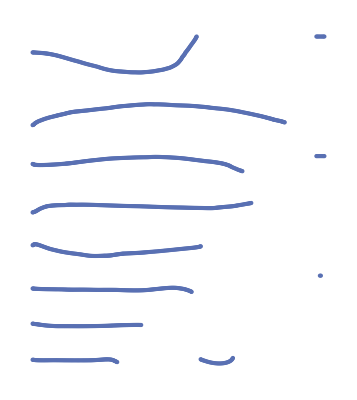

```mathematica
Graph[metaGraph]
```

```mathematica
groupedVertices=ConnectedComponents[metaGraph]
```

{{8801,5993,6000,8800,11367,5990,6003,8799,11366,2427,5991,8798,11340,5785,5992,11232,11339,5969,6001,8737,8733,5951,2371,11231,8711,6004,5941,11376,11331,5809,5934,8725,11300,8724,5944,8726,11302,5999,5886,11368,11301,5962,5936,8612,11313,5963,5901,8721,11291,2376,5943,8722,7043,2368,5902,8723,8968,5998,5940,6971,8719,387,5942,11342,8720,5985,5887,11343,11298,5964,5903,11346,8700,5967,5912,11353,8699,5979,2407,11354,11315,5957,394,11355,8614,5978,8613,11356,8615,5980,2359,11345,8717,5955,5898,11344,8775,5973,6990,11357,6991,5972,122,11223,8705,5781,5900,8730,8704,307,302,7839,8815,5977,5906,11177,8833,5960,6110,8589,8834,2373,6109,8588,11436,5971,6089,11175,8828,5956,2444,11162,11435,5665,2443,11164,11417,5664,2436,11163,11410,5655,11408,8532,11409,2413,2446,8315,8768,53,8830,8829,8831,700,7356,6111,11439,11438,11441,11440,11442,6114,8637,6113,11437,6122,11456,6123,8835,6115,6964,379,6963,6118,11452,2524,8960,6120,8823,6084,8822,2442,8820,6302,8805,6303,8804,2434,8931,6112,11411,6274,11597,6298,8827,6297,8826,6296,8825,8824,11444,11443,11458,2499,11455,6301,11606,6299,8959,6300,11605,6276,11600,11599,11601,6282,11577,6251,8933,6277,8932,404,8984,6278,8982,2430,8840,2509,8918,2535,8985,6280,8987,6279,11617,11616,11619,11618,11621,11620,11622,9678,9680,9679,9682,9681,9683,6386,8922,6321,8923,6322,11615,6393,8878,6391,8943,6390,8935},{8750,6056,6057,8751,11396,2271,6061,8790,11397,1966,6060,7375,8592,708,6063,7374,8593,6051,2397,8776,8476,2396,6064,11389,8736,374,2422,11391,11398,8649,5938,8650,8360,6054,2418,11387,11381,6038,6062,11388,11375,6037,5987,11390,11374,2342,6065,8666,11373,6041,6035,8667,11372,5884,6059,8696,11395,6036,6072,8695,11021,344,6071,6946,11358,6044,6069,6945,11399,6039,6070,8681,11363,6043,11361,8680,11362,6040,5652,8682,11160,6034,11159,11314,11161,6042,6011,11290,11189,6033,6067,11289,11181,5905,2424,11285,8794,5885,2425,8645,8795,6088,5281,8644,8796,441,6068,8665,10945,6325,5682,11297,8308,6342,5677,8662,8793,6344,5287,6987,10943,386,5678,8718,10944,2352,5684,8698,11188,8697,5644,11637,8324,6324,2023,11286,8362,6327,5292,11247,8363,11246,5286,11248,8372,6337,1973,11249,8325,6338,1980,11629,8326,6329,5290,11284,8331,6339,5293,11631,10966,6328,5311,11250,10952,5815,5297,8955,8371,6326,8369,11630,8370,6330,5288,11628,10965,6382,10963,11627,10964,6381,10961,11252,10962,6331,5303,11251,10953,6380,5298,8693,10973,8692,5285,8694,10958,6404,5309,9000,10959,1981,8332,5314,10957,5301,10956,5300,10954,5310,10824,5044,8387,2063,8514,5295,10951,5304,10955,5299,8537,5308},{9704,3302,3303,9667,9706,3305,3322,9705,9725,3323,6320,9726,8894,3327,8892,9727,8893,3326,2495,9710,8890,3321,9709,3307,9711,3299,9689,3298,9688,3295,9677,3290,9698,3300,9707,3320,9663,3328,9735,3297,9733,3329,9734,3463,9847,714,9846,77,9718,3461,8673,716,9696,715,9723,7381,7382,3452,7393,3483,7400,316,7397,705,7398,3499,9883,3494,9844,742,9829,3480,7385,717,7396,3482,7401,33,9841,3481,9863,3476,9864,3454,9819,3439,9828,3478,9827,9825,9826,3443,9824,3444,8712,3438,9816,3441,9818,3440,9821,3442,9817,3467,11335,5890,11333,5935,11334,5933,9836,3451,9832,5895,7377,7376,7378,5916,11308,3447,9830,5927,9831,5923,11326,5928,11327,5929,11328,5926,8708,3448,9833,5918,11309,5899,11312,5917,6982,402,9809,3428,8709,5909,11429,6097,11325,3336,11324,5919,11430,2440,8706,2355,8816,6104,8817,5914,11323,6103,11322,6107,11311,6099,9808,5915,11427,6096,6993,2349,6992,407,8954,6091,11419,6095,11424,11423,11425,5892,11426,6090,8946,6094,11418,6335,11636,6336,7017,2520,8949,8948,8951,8950,8952,6308,11611,6309,11610,6310,9744,6317,9743,9741,9742,6311,9739,3335,9740,826,7486,6307,7488,7487},{5851,8753,11279,5866,5867,8636,8651,5857,2327,8635,6689,2313,5865,8594,6688,5860,5787,11287,8663,5861,2339,11288,11229,5862,5864,8632,11228,5863,5882,8631,11230,2311,2317,8671,8641,378,5879,11275,8690,8608,5883,11274,8689,2305,2351,11276,8691,5846,5881,8627,8607,5834,5786,8626,11233,2310,5880,9136,6958,5818,2138,11266,8463,5835,5782,8969,8652,5853,2360,8936,11377,2518,6002,8944,11378,5814,6005,8945,11379,6356,2380,8966,8744,2528,6006,8965,8734,6597,6007,11832,11352,6600,5994,11837,11351,11835,2375,11836,11371,6602,5995,11834,11336,6601,5997,11661,8735,6603,2372,11720,6954,6604,5996,11719,11369,6434,5966,11709,11224,6439,2423,9010,8791,9008,5982,9009,8792,8604,5970,9030,11364,9029,5981,9032,11365,9031,5965,9033,8732,8988,2386,11712,7459,11710,2394,11711,11359,11699,5667,11700,11185,11697,5976,11698,8797,11245,5975,11694,8727,11693,5779,11695,6938,6431,342,11696,6939,6432,5968,9001,6940,5974,6941,5656,8590,2275,7854,2367,8533,2370,11165,5375,8395},{6778,133,4919,10271,8220,10270,4916,10272,8073,1268,4917,10247,8072,4937,1671,10248,6809,4936,4918,10249,10756,4930,10755,10774,10757,201,1686,10776,10268,4939,4116,10775,10269,4938,4902,8071,10743,4999,4945,8070,10744,5000,4942,8127,10778,1713,4940,8126,8095,5002,4941,10803,8101,4998,4101,7620,10250,989,1692,7621,8103,5004,8102,10804,8104,5010,1693,6826,10738,5001,4944,8133,8089,1695,4893,8106,6885,4929,4943,10766,8081,5009,270,10767,10736,5011,4921,10768,10735,1712,10734,10769,10737,4994,4894,8123,10739,4895,8099,8097,8098,4891,7619,4889,10747,4884,10748,4915,10754,4880,10752,4920,10730,4908,8045,1639,10751,4947,8085,4923,8084,1670,10762,4946,10759,4922,10758,1672,8060,1649,7583,932,7582,4933,8054,1647,6785,152,6829,4932,8105,4038,10204,4090,6864,4048,7896,4924,8128,4934,10770,1599,10196,5005,10805,1701,8107,4996,10771,1674,8080,5003,10772,1667,10806,5007,10807,5006,10798,4989,10777,4983,8129},{5019,10239,10240,4084,4979,10788,7872,1728,5022,8183,8385,2066,5021,8184,8341,4956,5020,10781,8391,4964,1997,10782,6918,1719,2065,8139,6917,1984,5338,8140,6915,1004,5018,7635,6916,4965,5389,7634,11025,4958,5393,8110,8179,4963,5397,8111,8178,4072,5392,10232,8177,1694,1754,6673,8176,6671,2067,6672,8558,4967,2070,6665,8555,18,5028,6666,10816,4970,5379,6667,11024,1710,5399,8121,8556,4953,5400,8118,11026,8116,5394,8117,10980,4976,1994,10629,10981,4977,5395,8092,8389,4968,5396,10790,8345,4973,5398,10243,8344,4961,1999,10783,10997,4972,5388,10780,10988,4950,5335,10784,10987,4794,5327,10686,10996,4978,10994,10687,10995,4959,10992,10688,10993,4971,5331,10689,10990,4833,5324,10690,10991,4975,5317,10791,8340,1783,5325,10218,10998,4980,5334,10795,10999,4993,5332,10792,10982,4974,5333,10793,10971,4995,5342,10794,11000,4949,8130,4827,8158,4992,8113},{5030,8189,8191,1766,4962,8147,10809,1727,5034,10810,10811,5032,5039,10786,10796,2064,5036,8390,10817,5024,5037,8192,8143,5025,5023,7826,8144,1265,5031,7863,10813,5029,1724,7864,8119,5027,1700,8174,7636,4553,1005,8173,8137,5390,4955,10815,8141,5391,4951,10814,8142,5321,4952,6900,10819,298,5038,6901,10224,5322,5016,8392,10797,1342,1698,8193,6876,1976,1717,8186,6875,1760,259,10984,6877,1988,4986,8337,8078,2058,1702,8327,8077,5320,1673,8171,8079,273,4987,8393,10799,1749,4985,8394,10219,5336,4981,8138,8154,2061,1715,8114,8131,1990,8339,5330,10969,5337,8109,1697},{1972,8540,8541,5692,5316,8538,10977,2235,2208,8539,10972,5693,5312,11193,8346,5694,5339,10960,8347,5315,5344,8115,11001,2225,5326,10974,10985,5345,5346,9977,10986,5696,2232,8317,10975,5689,5313,11195,8323,5699,5328,8375,8322,2228,8542,5698,8543,5662,10976,5700,9978,5701,7366,5680,7364,2227,7365,5660,11178,5688,11179,5686,11167,5679,11169,11168,11171,11170,11172,5663,11182,787,7451,5672,7452,5671,8529,5653,6907,5666,11183,5669,11184,5670,8504,2192,8314},{9664,6421,6423,11708,9665,6419,6422,11675,8940,6420,6394,11676,11257,6418,6385,7304,11258,6379,6384,9692,9003,9690,6397,9691,9002,8813,8814,8811,8812,6332,9729,9728,9730,7490,7491,7489},{1664,8134,10779,1711,4954,8112,8125,4948,8124},{2000,9974,9975,5329,9976,1720,1993,8388,5341},{7492,8934}}

```mathematica
groupedEdges=Table[Flatten[Cases[metaGraph,#<->_]&/@groupedVertices⟦i⟧],{i,1,Length[groupedVertices]}]
```

{{5993<->8800,5993<->8801,6000<->8801,6000<->11367,5990<->8799,5990<->8800,6003<->11366,6003<->11367,2427<->8798,2427<->8799,5991<->11340,5991<->11366,5785<->8798,5785<->11232,5992<->11339,5992<->11340,5969<->8737,5969<->11232,6001<->8733,6001<->11339,5951<->8737,5951<->11231,2371<->8711,2371<->8733,6004<->11231,6004<->11376,5941<->8711,5941<->11331,5809<->8725,5809<->11376,5934<->11300,5934<->11331,8724<->8725,8724<->8726,5944<->11300,5944<->11302,5999<->8726,5999<->11368,5886<->11301,5886<->11302,5962<->8612,5962<->11368,5936<->11301,5936<->11313,5963<->8612,5963<->8721,5901<->11291,5901<->11313,2376<->8721,2376<->8722,5943<->7043,5943<->11291,2368<->8722,2368<->8723,5902<->7043,5902<->8968,5998<->6971,5998<->8723,5940<->8719,5940<->8968,387<->6971,387<->11342,5942<->8719,5942<->8720,5985<->11342,5985<->11343,5887<->8720,5887<->11298,5964<->11343,5964<->11346,5903<->8700,5903<->11298,5967<->11346,5967<->11353,5912<->8699,5912<->8700,5979<->11353,5979<->11354,2407<->8699,2407<->11315,5957<->11354,5957<->11355,394<->8614,394<->11315,5978<->11355,5978<->11356,8613<->8614,8613<->8615,5980<->11345,5980<->11356,2359<->8615,2359<->8717,5955<->11344,5955<->11345,5898<->8717,5898<->8775,5973<->11344,5973<->11357,6990<->6991,6990<->8775,5972<->11223,5972<->11357,122<->6991,122<->8705,5781<->8730,5781<->11223,5900<->8704,5900<->8705,307<->7839,307<->8730,302<->8704,302<->8815,5977<->7839,5977<->11177,5906<->8815,5906<->8833,5960<->8589,5960<->11177,6110<->8833,6110<->8834,2373<->8588,2373<->8589,6109<->8834,6109<->11436,5971<->8588,5971<->11175,6089<->8828,6089<->11436,5956<->11162,5956<->11175,2444<->8828,2444<->11435,5665<->11162,5665<->11164,2443<->11417,2443<->11435,5664<->11163,5664<->11164,2436<->11410,2436<->11417,5655<->8532,5655<->11163,11408<->11409,11408<->11410,2413<->8315,2413<->8532,2446<->8768,2446<->11409,53<->8768,53<->8830,8829<->8830,8829<->8831,700<->7356,700<->8831,6111<->7356,6111<->11439,11438<->11439,11438<->11441,11440<->11441,11440<->11442,6114<->8637,6114<->11442,6113<->8637,6113<->11437,6122<->11437,6122<->11456,6123<->8835,6123<->11456,6115<->6964,6115<->8835,379<->6963,379<->6964,6118<->6963,6118<->11452,2524<->8960,2524<->11452,6120<->8823,6120<->8960,6084<->8822,6084<->8823,2442<->8820,2442<->8822,6302<->8805,6302<->8820,6303<->8804,6303<->8805,2434<->8804,2434<->8931,6112<->8931,6112<->11411,6274<->11411,6274<->11597,6298<->8827,6298<->11597,6297<->8826,6297<->8827,6296<->8825,6296<->8826,8824<->8825,8824<->11444,11443<->11444,11443<->11458,2499<->11455,2499<->11458,6301<->11455,6301<->11606,6299<->8959,6299<->11606,6300<->8959,6300<->11605,6276<->11600,6276<->11605,11599<->11600,11599<->11601,6282<->11577,6282<->11601,6251<->8933,6251<->11577,6277<->8932,6277<->8933,404<->8932,404<->8984,6278<->8982,6278<->8984,2430<->8840,2430<->8982,2509<->8840,2509<->8918,2535<->8918,2535<->8985,6280<->8985,6280<->8987,6279<->8987,6279<->11617,11616<->11617,11616<->11619,11618<->11619,11618<->11621,11620<->11621,11620<->11622,9678<->9680,9678<->11622,9679<->9680,9679<->9682,9681<->9682,9681<->9683,6386<->8922,6386<->9683,6321<->8922,6321<->8923,6322<->8923,6322<->11615,6393<->8878,6393<->11615,6391<->8878,6391<->8943,6390<->8935,6390<->8943},{6056<->8750,6056<->8751,6057<->8750,6057<->11396,2271<->8751,2271<->8790,6061<->11396,6061<->11397,1966<->7375,1966<->8790,6060<->8592,6060<->11397,708<->7374,708<->7375,6063<->8592,6063<->8593,6051<->7374,6051<->8776,2397<->8476,2397<->8593,2396<->8776,2396<->11389,6064<->8476,6064<->8736,374<->11389,374<->11391,2422<->8736,2422<->11398,8649<->8650,8649<->11391,5938<->8360,5938<->11398,6054<->8650,6054<->11387,2418<->8360,2418<->11381,6038<->11387,6038<->11388,6062<->11375,6062<->11381,6037<->11388,6037<->11390,5987<->11374,5987<->11375,2342<->8666,2342<->11390,6065<->11373,6065<->11374,6041<->8666,6041<->8667,6035<->11372,6035<->11373,5884<->8667,5884<->8696,6059<->11372,6059<->11395,6036<->8695,6036<->8696,6072<->11021,6072<->11395,344<->6946,344<->8695,6071<->11021,6071<->11358,6044<->6945,6044<->6946,6069<->11358,6069<->11399,6039<->6945,6039<->8681,6070<->11363,6070<->11399,6043<->8680,6043<->8681,11361<->11362,11361<->11363,6040<->8680,6040<->8682,5652<->11160,5652<->11362,6034<->8682,6034<->11314,11159<->11160,11159<->11161,6042<->11290,6042<->11314,6011<->11161,6011<->11189,6033<->11289,6033<->11290,6067<->11181,6067<->11189,5905<->11285,5905<->11289,2424<->8794,2424<->11181,5885<->8645,5885<->11285,2425<->8794,2425<->8795,6088<->8644,6088<->8645,5281<->8795,5281<->8796,441<->8644,441<->8665,6068<->8796,6068<->10945,6325<->8665,6325<->11297,5682<->8308,5682<->10945,6342<->8662,6342<->11297,5677<->8308,5677<->8793,6344<->6987,6344<->8662,5287<->8793,5287<->10943,386<->6987,386<->8718,5678<->10943,5678<->10944,2352<->8698,2352<->8718,5684<->10944,5684<->11188,8697<->8698,8697<->11637,5644<->8324,5644<->11188,6324<->11286,6324<->11637,2023<->8324,2023<->8362,6327<->11247,6327<->11286,5292<->8362,5292<->8363,11246<->11247,11246<->11248,5286<->8363,5286<->8372,6337<->11248,6337<->11249,1973<->8325,1973<->8372,6338<->11249,6338<->11629,1980<->8325,1980<->8326,6329<->11284,6329<->11629,5290<->8326,5290<->8331,6339<->11284,6339<->11631,5293<->8331,5293<->10966,6328<->11250,6328<->11631,5311<->10952,5311<->10966,5815<->8955,5815<->11250,5297<->8371,5297<->10952,6326<->8955,6326<->11630,8369<->8370,8369<->8371,6330<->11628,6330<->11630,5288<->8370,5288<->10965,6382<->11627,6382<->11628,10963<->10964,10963<->10965,6381<->11252,6381<->11627,10961<->10962,10961<->10964,6331<->11251,6331<->11252,5303<->10953,5303<->10962,6380<->8693,6380<->11251,5298<->10953,5298<->10973,8692<->8693,8692<->8694,5285<->10958,5285<->10973,6404<->8694,6404<->9000,5309<->10958,5309<->10959,1981<->8332,1981<->10959,5314<->8332,5314<->10957,5301<->10956,5301<->10957,5300<->10954,5300<->10956,5310<->10824,5310<->10954,5044<->8387,5044<->10824,2063<->8387,2063<->8514,5295<->8514,5295<->10951,5304<->10951,5304<->10955,5299<->8537,5299<->10955,5308<->8537},{3302<->9667,3302<->9704,3303<->9704,3303<->9706,3305<->9667,3305<->9705,3322<->9706,3322<->9725,3323<->9705,3323<->9726,6320<->8894,6320<->9725,3327<->9726,3327<->9727,8892<->8893,8892<->8894,3326<->9710,3326<->9727,2495<->8890,2495<->8893,3321<->9709,3321<->9710,3307<->9709,3307<->9711,3299<->9689,3299<->9711,3298<->9688,3298<->9689,3295<->9677,3295<->9688,3290<->9677,3290<->9698,3300<->9698,3300<->9707,3320<->9663,3320<->9707,3328<->9663,3328<->9735,3297<->9733,3297<->9735,3329<->9733,3329<->9734,3463<->9734,3463<->9847,714<->9846,714<->9847,77<->9718,77<->9846,3461<->8673,3461<->9718,716<->8673,716<->9696,715<->9696,715<->9723,7381<->7382,7381<->9723,3452<->7382,3452<->7393,3483<->7393,3483<->7400,316<->7397,316<->7400,705<->7397,705<->7398,3499<->7398,3499<->9883,3494<->9844,3494<->9883,742<->9829,742<->9844,3480<->7385,3480<->9829,717<->7385,717<->7396,3482<->7396,3482<->7401,33<->7401,33<->9841,3481<->9841,3481<->9863,3476<->9863,3476<->9864,3454<->9819,3454<->9864,3439<->9819,3439<->9828,3478<->9827,3478<->9828,9825<->9826,9825<->9827,3443<->9824,3443<->9826,3444<->8712,3444<->9824,3438<->8712,3438<->9816,3441<->9816,3441<->9818,3440<->9818,3440<->9821,3442<->9817,3442<->9821,3467<->9817,3467<->11335,5890<->11333,5890<->11335,5935<->11333,5935<->11334,5933<->9836,5933<->11334,3451<->9832,3451<->9836,5895<->7377,5895<->9832,7376<->7377,7376<->7378,5916<->7378,5916<->11308,3447<->9830,3447<->11308,5927<->9830,5927<->9831,5923<->9831,5923<->11326,5928<->11326,5928<->11327,5929<->11327,5929<->11328,5926<->8708,5926<->11328,3448<->8708,3448<->9833,5918<->9833,5918<->11309,5899<->11309,5899<->11312,5917<->6982,5917<->11312,402<->6982,402<->9809,3428<->8709,3428<->9809,5909<->8709,5909<->11429,6097<->11325,6097<->11429,3336<->11324,3336<->11325,5919<->11324,5919<->11430,2440<->8706,2440<->11430,2355<->8706,2355<->8816,6104<->8816,6104<->8817,5914<->8817,5914<->11323,6103<->11322,6103<->11323,6107<->11311,6107<->11322,6099<->9808,6099<->11311,5915<->9808,5915<->11427,6096<->6993,6096<->11427,2349<->6992,2349<->6993,407<->6992,407<->8954,6091<->8954,6091<->11419,6095<->11419,6095<->11424,11423<->11424,11423<->11425,5892<->11425,5892<->11426,6090<->8946,6090<->11426,6094<->8946,6094<->11418,6335<->11418,6335<->11636,6336<->7017,6336<->11636,2520<->7017,2520<->8949,8948<->8949,8948<->8951,8950<->8951,8950<->8952,6308<->8952,6308<->11611,6309<->11610,6309<->11611,6310<->9744,6310<->11610,6317<->9743,6317<->9744,9741<->9742,9741<->9743,6311<->9739,6311<->9742,3335<->9739,3335<->9740,826<->7486,826<->9740,6307<->7486,6307<->7488,7487<->7488},{5851<->8753,5851<->11279,5866<->8636,5866<->8753,5867<->8651,5867<->11279,5857<->8635,5857<->8636,2327<->6689,2327<->8651,2313<->8594,2313<->8635,5865<->6688,5865<->6689,5860<->8594,5860<->11287,5787<->6688,5787<->8663,5861<->11287,5861<->11288,2339<->8663,2339<->11229,5862<->8632,5862<->11288,5864<->11228,5864<->11229,5863<->8631,5863<->8632,5882<->11228,5882<->11230,2311<->8631,2311<->8671,2317<->8641,2317<->11230,378<->8671,378<->11275,5879<->8641,5879<->8690,8608<->11274,8608<->11275,5883<->8689,5883<->8690,2305<->11274,2305<->11276,2351<->8689,2351<->8691,5846<->8627,5846<->11276,5881<->8607,5881<->8691,5834<->8626,5834<->8627,5786<->8607,5786<->11233,2310<->8626,2310<->9136,5880<->6958,5880<->11233,5818<->9136,5818<->11266,2138<->6958,2138<->8463,5835<->8969,5835<->11266,5782<->8463,5782<->8652,5853<->8936,5853<->8969,2360<->8652,2360<->11377,2518<->8936,2518<->8944,6002<->11377,6002<->11378,5814<->8944,5814<->8945,6005<->11378,6005<->11379,6356<->8945,6356<->8966,2380<->8744,2380<->11379,2528<->8965,2528<->8966,6006<->8734,6006<->8744,6597<->8965,6597<->11832,6007<->8734,6007<->11352,6600<->11832,6600<->11837,5994<->11351,5994<->11352,11835<->11836,11835<->11837,2375<->11351,2375<->11371,6602<->11834,6602<->11836,5995<->11336,5995<->11371,6601<->11661,6601<->11834,5997<->8735,5997<->11336,6603<->11661,6603<->11720,2372<->6954,2372<->8735,6604<->11719,6604<->11720,5996<->6954,5996<->11369,6434<->11709,6434<->11719,5966<->11224,5966<->11369,6439<->9010,6439<->11709,2423<->8791,2423<->11224,9008<->9009,9008<->9010,5982<->8791,5982<->8792,8604<->9009,8604<->9030,5970<->8792,5970<->11364,9029<->9030,9029<->9032,5981<->11364,5981<->11365,9031<->9032,9031<->9033,5965<->8732,5965<->11365,8988<->9033,8988<->11712,2386<->7459,2386<->8732,11710<->11711,11710<->11712,2394<->7459,2394<->11359,11699<->11700,11699<->11711,5667<->11185,5667<->11359,11697<->11698,11697<->11700,5976<->8797,5976<->11185,11245<->11694,11245<->11698,5975<->8727,5975<->8797,11693<->11694,11693<->11695,5779<->6938,5779<->8727,6431<->11695,6431<->11696,342<->6938,342<->6939,6432<->9001,6432<->11696,5968<->6939,5968<->6940,5974<->6940,5974<->6941,5656<->6941,5656<->8590,2275<->7854,2275<->8590,2367<->7854,2367<->8533,2370<->8533,2370<->11165,5375<->8395,5375<->11165},{133<->6778,133<->10271,4919<->6778,4919<->8220,10270<->10271,10270<->10272,4916<->8073,4916<->8220,1268<->10247,1268<->10272,4917<->8072,4917<->8073,4937<->10247,4937<->10248,1671<->6809,1671<->8072,4936<->10248,4936<->10249,4918<->6809,4918<->10756,4930<->10249,4930<->10774,10755<->10756,10755<->10757,201<->10774,201<->10776,1686<->10268,1686<->10757,4939<->10775,4939<->10776,4116<->10268,4116<->10269,4938<->8071,4938<->10775,4902<->10269,4902<->10743,4999<->8070,4999<->8071,4945<->10743,4945<->10744,5000<->8070,5000<->8127,4942<->10744,4942<->10778,1713<->8126,1713<->8127,4940<->8095,4940<->10778,5002<->8126,5002<->10803,4941<->8095,4941<->8101,4998<->7620,4998<->10803,4101<->8101,4101<->10250,989<->7620,989<->7621,1692<->8103,1692<->10250,5004<->7621,5004<->10804,8102<->8103,8102<->8104,5010<->6826,5010<->10804,1693<->8104,1693<->10738,5001<->6826,5001<->8133,4944<->8089,4944<->10738,1695<->8106,1695<->8133,4893<->6885,4893<->8089,4929<->8106,4929<->10766,4943<->6885,4943<->8081,5009<->10766,5009<->10767,270<->8081,270<->10736,5011<->10767,5011<->10768,4921<->10735,4921<->10736,1712<->10768,1712<->10769,10734<->10735,10734<->10737,4994<->8123,4994<->10769,4894<->10737,4894<->10739,4895<->8099,4895<->10739,8097<->8098,8097<->8099,4891<->7619,4891<->8098,4889<->7619,4889<->10747,4884<->10747,4884<->10748,4915<->10748,4915<->10754,4880<->10752,4880<->10754,4920<->10730,4920<->10752,4908<->8045,4908<->10730,1639<->8045,1639<->10751,4947<->8085,4947<->10751,4923<->8084,4923<->8085,1670<->8084,1670<->10762,4946<->10759,4946<->10762,4922<->10758,4922<->10759,1672<->8060,1672<->10758,1649<->7583,1649<->8060,932<->7582,932<->7583,4933<->7582,4933<->8054,1647<->6785,1647<->8054,152<->6785,152<->6829,4932<->6829,4932<->8105,4038<->8105,4038<->10204,4090<->6864,4090<->10204,4048<->6864,4048<->7896,4924<->7896,4924<->8128,4934<->8128,4934<->10770,1599<->10196,1599<->10770,5005<->10196,5005<->10805,1701<->8107,1701<->10805,4996<->8107,4996<->10771,1674<->8080,1674<->10771,5003<->8080,5003<->10772,1667<->10772,1667<->10806,5007<->10806,5007<->10807,5006<->10798,5006<->10807,4989<->10777,4989<->10798,4983<->8129,4983<->10777},{5019<->10239,5019<->10240,4084<->10239,4084<->10788,4979<->7872,4979<->10240,1728<->8183,1728<->10788,5022<->7872,5022<->8385,2066<->8183,2066<->8184,5021<->8341,5021<->8385,4956<->8184,4956<->10781,5020<->8341,5020<->8391,4964<->10781,4964<->10782,1997<->6918,1997<->8391,1719<->8139,1719<->10782,2065<->6917,2065<->6918,1984<->8139,1984<->8140,5338<->6915,5338<->6917,1004<->7635,1004<->8140,5018<->6915,5018<->6916,4965<->7634,4965<->7635,5389<->6916,5389<->11025,4958<->7634,4958<->8110,5393<->8179,5393<->11025,4963<->8110,4963<->8111,5397<->8178,5397<->8179,4072<->8111,4072<->10232,5392<->8177,5392<->8178,1694<->6673,1694<->10232,1754<->8176,1754<->8177,6671<->6672,6671<->6673,2067<->8176,2067<->8558,4967<->6665,4967<->6672,2070<->8555,2070<->8558,18<->6665,18<->6666,5028<->8555,5028<->10816,4970<->6666,4970<->6667,5379<->10816,5379<->11024,1710<->6667,1710<->8121,5399<->8556,5399<->11024,4953<->8118,4953<->8121,5400<->8556,5400<->11026,8116<->8117,8116<->8118,5394<->10980,5394<->11026,4976<->8117,4976<->10629,1994<->10980,1994<->10981,4977<->8092,4977<->10629,5395<->8389,5395<->10981,4968<->8092,4968<->10790,5396<->8345,5396<->8389,4973<->10243,4973<->10790,5398<->8344,5398<->8345,4961<->10243,4961<->10783,1999<->8344,1999<->10997,4972<->10780,4972<->10783,5388<->10988,5388<->10997,4950<->10780,4950<->10784,5335<->10987,5335<->10988,4794<->10686,4794<->10784,5327<->10987,5327<->10996,4978<->10686,4978<->10687,10994<->10995,10994<->10996,4959<->10687,4959<->10688,10992<->10993,10992<->10995,4971<->10688,4971<->10689,5331<->10990,5331<->10993,4833<->10689,4833<->10690,5324<->10990,5324<->10991,4975<->10690,4975<->10791,5317<->8340,5317<->10991,1783<->10218,1783<->10791,5325<->8340,5325<->10998,4980<->10218,4980<->10795,5334<->10998,5334<->10999,4993<->10792,4993<->10795,5332<->10982,5332<->10999,4974<->10792,4974<->10793,5333<->10971,5333<->10982,4995<->10793,4995<->10794,5342<->10971,5342<->11000,4949<->8130,4949<->10794,4827<->8130,4827<->8158,4992<->8113,4992<->8158},{5030<->8189,5030<->8191,1766<->8147,1766<->8189,4962<->8191,4962<->10809,1727<->8147,1727<->10810,5034<->10809,5034<->10811,5032<->10786,5032<->10810,5039<->10796,5039<->10811,2064<->8390,2064<->10786,5036<->10796,5036<->10817,5024<->8192,5024<->8390,5037<->8143,5037<->10817,5025<->7826,5025<->8192,5023<->8143,5023<->8144,1265<->7826,1265<->7863,5031<->8144,5031<->10813,5029<->7863,5029<->7864,1724<->8119,1724<->10813,5027<->7864,5027<->8174,1700<->7636,1700<->8119,4553<->8173,4553<->8174,1005<->7636,1005<->8137,5390<->8173,5390<->10815,4955<->8137,4955<->8141,5391<->10814,5391<->10815,4951<->8141,4951<->8142,5321<->6900,5321<->10814,4952<->8142,4952<->10819,298<->6900,298<->6901,5038<->10224,5038<->10819,5322<->6901,5322<->8392,5016<->10224,5016<->10797,1342<->8193,1342<->8392,1698<->6876,1698<->10797,1976<->8186,1976<->8193,1717<->6875,1717<->6876,1760<->8186,1760<->10984,259<->6875,259<->6877,1988<->8337,1988<->10984,4986<->6877,4986<->8078,2058<->8327,2058<->8337,1702<->8077,1702<->8078,5320<->8171,5320<->8327,1673<->8077,1673<->8079,273<->8171,273<->8393,4987<->8079,4987<->10799,1749<->8393,1749<->8394,4985<->10219,4985<->10799,5336<->8138,5336<->8394,4981<->8154,4981<->10219,2061<->8114,2061<->8138,1715<->8131,1715<->8154,1990<->8114,1990<->8339,5330<->8339,5330<->10969,5337<->8109,5337<->10969,1697<->8109},{1972<->8540,1972<->8541,5692<->8538,5692<->8540,5316<->8541,5316<->10977,2235<->8538,2235<->8539,2208<->10972,2208<->10977,5693<->8539,5693<->11193,5312<->8346,5312<->10972,5694<->10960,5694<->11193,5339<->8346,5339<->8347,5315<->8115,5315<->10960,5344<->8347,5344<->11001,2225<->8115,2225<->10974,5326<->10985,5326<->11001,5345<->9977,5345<->10974,5346<->10985,5346<->10986,5696<->8317,5696<->9977,2232<->10975,2232<->10986,5689<->8317,5689<->11195,5313<->8323,5313<->10975,5699<->8375,5699<->11195,5328<->8322,5328<->8323,2228<->8375,2228<->8542,5698<->8542,5698<->8543,5662<->8543,5662<->10976,5700<->9978,5700<->10976,5701<->7366,5701<->9978,5680<->7364,5680<->7366,2227<->7364,2227<->7365,5660<->7365,5660<->11178,5688<->11178,5688<->11179,5686<->11167,5686<->11179,5679<->11167,5679<->11169,11168<->11169,11168<->11171,11170<->11171,11170<->11172,5663<->11172,5663<->11182,787<->7451,787<->11182,5672<->7451,5672<->7452,5671<->7452,5671<->8529,5653<->6907,5653<->8529,5666<->6907,5666<->11183,5669<->11183,5669<->11184,5670<->8504,5670<->11184,2192<->8314,2192<->8504},{6421<->9664,6421<->11708,6423<->9664,6423<->9665,6419<->11675,6419<->11708,6422<->8940,6422<->9665,6420<->11675,6420<->11676,6394<->8940,6394<->11257,6418<->7304,6418<->11676,6385<->11257,6385<->11258,6379<->7304,6379<->9692,6384<->9003,6384<->11258,9690<->9691,9690<->9692,6397<->9002,6397<->9003,8813<->8814,8813<->9691,8811<->8812,8811<->8814,6332<->8812,6332<->9729,9728<->9729,9728<->9730,7490<->7491,7490<->9730,7489<->7491},{1664<->8134,1664<->10779,1711<->8112,1711<->8134,4954<->8125,4954<->10779,4948<->8124,4948<->8125},{2000<->9974,2000<->9975,5329<->9975,5329<->9976,1720<->1993,1720<->9976,1993<->8388,5341<->8388},{7492<->8934}}

```mathematica
Length/@groupedEdges
```

{258,221,213,182,172,160,109,86,35,8,8,1}

```mathematica
Length/@groupedVertices
```

{259,222,214,183,173,161,110,87,36,9,9,2}